Created by: ruebenko on 11-15-2019 14:58:20

### Categorization

Tutorial

OpenCascadeLink

OpenCascadeLink`

OpenCascadeLink/tutorial/UsingOpenCascadeLink

Synonyms

CAD

### Keywords

CAD

surface mesh

ElementMesh

Boundary ElementMesh

Boolean

Boolean operation

RegionDifference

RegionUnion

RegionIntersection

rotation

region rotation

translation

region translation

BSpline

BSplineSurface

BSplineFunction

Filet

Filets

Healing

Shape

Shape Healing

Shape fixing

Chamfer

Chamfers

Shell

Shelling

step

step import

step export

stp

stp import

stp export

Details

# Using OpenCascadeLink

This notebook has TrackCellChangeTimes -> False set.

This notebook has FileOutlineCache -> False set.

SetOptions[InputNotebook[],PrivateNotebookOptions→{"FileOutlineCache"→False},TrackCellChangeTimes→False]

This section shows some of the ways that OpenCascadeLink can be applied. To use OpenCascadeLink, it must first be loaded.

```mathematica
Needs["OpenCascadeLink`"]
```

Since many of the OpenCascade examples interact with the finite element mesh functionality the finite element package is also loaded.

```mathematica
Needs["NDSolve`FEM`"]
```

## OpenCascade Primitives

The first step is to create OpenCascade objects. There are several ways of doing this. For 3D objects the options are to:

Convert solid graphics 3D primitives

Additional OpenCascade 3D primitives

Convert surface graphics primitives

Convert surface meshes

Convert edge graphics primitives

Additional OpenCascade edge primitives

Create Surfaces from Edges

Working with 2D graphics primitives the possibility are to:

Convert solid graphics 2D primitives

Convert boundary graphics primitives

### Solid 3D Primitives

Various Wolfram Language Graphics3D primitives can be represented in OpenCascade. These primitives are represented as solids.

#### Ball

Create two distinct Ball primitives in OpenCascade.

```mathematica
shape1=OpenCascadeShape[Ball[{1,0,0}]]
shape2=OpenCascadeShape[Ball[{0,1/2,0},1/2]]
```

OpenCascadeShapeExpression[1]

OpenCascadeShapeExpression[2]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape1]
```

Solid

Generate a boundary ElementMesh from the first OpenCascade shape.

```mathematica
bmesh1=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape1]
```

ElementMesh[{{0.,2.},{-1.,1.},{-1.,1.}},Automatic]

Generate a boundary ElementMesh from the second OpenCascade shape.

```mathematica
bmesh2=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape2]
```

ElementMesh[{{-0.5,0.5},{0.,1.},{-0.5,0.5}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
Show[bmesh1["Wireframe"],bmesh2["Wireframe"]]
```

-Graphics3D-

Generate the full ElementMesh.

```mathematica
ToElementMesh[bmesh1]
ToElementMesh[bmesh2]
```

ElementMesh[{{0.,2.},{-1.,1.},{-1.,1.}},{TetrahedronElement[<8041>]}]

ElementMesh[{{-0.5,0.5},{0.,1.},{-0.5,0.5}},{TetrahedronElement[<8083>]}]

Generate several Ball primitives in OpenCascade.

```mathematica
OpenCascadeShape[Ball[RandomReal[{-1,1},{4,3}]]]
```

{OpenCascadeShapeExpression[3],OpenCascadeShapeExpression[4],OpenCascadeShapeExpression[5],OpenCascadeShapeExpression[6]}

#### CapsuleShape

Create a CapsuleShape primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[CapsuleShape[{{0,-2,0},{0,0,1}},1]]
```

OpenCascadeShapeExpression[12]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-0.996584,1.},{-2.99112,0.993843},{-1.,2.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Cone

Create a Cone primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[Cone[{{0,0,0},{0,0,1}},1]]
```

OpenCascadeShapeExpression[13]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,1.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Cuboid

Create a Cuboid primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[Cuboid[{0,0,0},{1,2,3}]]
```

OpenCascadeShapeExpression[14]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,1.},{0.,2.},{0.,3.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Cylinder

Create a Cylinder primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[c1=Cylinder[{{0,0,0},{1,2,3}},1/2]]
```

OpenCascadeShapeExpression[15]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-0.478299,1.4783},{-0.421675,2.42168},{-0.297253,3.29725}},Automatic]

Visualize the boundary ElementMesh and the graphics primitive.

```mathematica
Show[bmesh["Wireframe"], Graphics3D[c1]]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Ellipsoid

Create a Ellipsoid primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[el1=Ellipsoid[{0,0,0},{{5,2,3},{2,3,2},{3,2,5}}]]
```

OpenCascadeShapeExpression[25]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-2.23533,2.23533},{-1.73113,1.73113},{-2.22808,2.22808}},Automatic]

Visualize the boundary ElementMesh and the graphics primitive.

```mathematica
Show[bmesh["Wireframe"], Graphics3D[el1]]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### FilledTorus

Create a FilledTorus primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[ft=FilledTorus[]]
```

OpenCascadeShapeExpression[26]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-0.994869,1.},{-0.998717,0.998717},{-0.248177,0.248177}},Automatic]

Visualize the boundary ElementMesh and the graphics primitive.

```mathematica
Show[bmesh["Wireframe"], Graphics3D[ft]]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Hexahedron

Create a Hexahedron primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}]]
```

OpenCascadeShapeExpression[33]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,2.},{0.,1.},{0.,1.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Parallelepiped

Create a Parallelepiped primitive in OpenCascade.

```mathematica
p=Parallelepiped[{1,0,0},{{1,0,0},{1,2,1},{0,1,1}}];
shape=OpenCascadeShape[p]
```

OpenCascadeShapeExpression[35]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Extract and visualize the boundary mesh and the Parallelepiped.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
Show[
Graphics3D[{Opacity[0.25],p}],
bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

#### Prism

Create a Prism primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[prism=Prism[{{1,0,1},{0,0,0},{2,0,0},{1,2,1},{0,2,0},{2,2,0}}]]
```

OpenCascadeShapeExpression[36]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,2.},{0.,2.},{0.,1.}},Automatic]

Visualize the boundary ElementMesh and the graphics primitive.

```mathematica
Show[bmesh["Wireframe"],Graphics3D[prism]]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Polyhedron

Create a Polyhedron primitive in OpenCascade.

```mathematica
polyhedron=Polyhedron[…];
shape=OpenCascadeShape[polyhedron]
```

OpenCascadeShapeExpression[58]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-1.37638,1.37638},{-1.30902,1.30902},{-1.11352,1.11352}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh,"RegionHoles"->{{0,0,0}}]["Wireframe"["MeshElement"->"MeshElements","MeshElementStyle"->Directive[{FaceForm[Orange],EdgeForm[]}],PlotRange->{{-1.5,1.5},{0,1.5},{-1.2,1.2}}]]
```

-Graphics3D-

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9421782191825606, 0.30641263512073286, 0.4240683037641967],RGBColor[0.9821364383651212, 0.5110172702414657, 0.6498306075283933],RGBColor[0.48257497002277205, 0.39367926979505186, 0.99991863793083],RGBColor[0.6308358608594066, 0.5593312522653415, 0.9997714945145527],RGBColor[0.7790967516960411, 0.7249832347356311, 0.9996243510982755],RGBColor[0.2783138319842018, 0.7738937595224964, 1.],RGBColor[0.48147635933747257, 0.8599097889839704, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.4220656343531402, 0.9800450002028409, 0.2855736924178059],RGBColor[0.6091400306115944, 0.9924863936620901, 0.45551440491106865],RGBColor[0.9763442441468795, 0.9438805446782267, 0.25189698675190353],RGBColor[0.9866205624332851, 0.9581441900989159, 0.4023413079796949],RGBColor[0.9968968807196906, 0.9724078355196053, 0.5527856292074862],RGBColor[1., 0.564994369252848, 0.1298465177047566],RGBColor[1., 0.657373184626424, 0.31551475885237834]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors,PlotRange->{{-1.5,1.5},{0,1.5},{-1.2,1.2}}]]
```

-Graphics3D-

Create a Polyhedron primitive in OpenCascade.

```mathematica
r1=TransformedRegion[Cuboid[],RotationTransform[Pi/8,{1,0,0}]];
r2=TransformedRegion[Cuboid[],RotationTransform[Pi/8,{0,1,0}]];
polyhedron=RegionUnion[r1,r2];
shape=OpenCascadeShape[polyhedron]
```

OpenCascadeShapeExpression[84]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,1.30656},{-0.382683,1.},{-0.382683,1.30656}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"["MeshElement"->"MeshElements","MeshElementStyle"->Directive[{FaceForm[Orange],EdgeForm[LightGray]}]]]
```

-Graphics3D-

#### Pyramid

Create a Pyramid primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}]]
```

OpenCascadeShapeExpression[90]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,2.},{0.,2.},{0.,2.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### SphericalShell

Create a SphericalShell primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[SphericalShell[]]
```

OpenCascadeShapeExpression[94]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-1.,1.},{-1.,1.},{-1.,1.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Mesh the region while keeping a region hole. Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh,"RegionHoles"->{{0,0,0}}]["Wireframe"]
```

-Graphics3D-

#### Tetrahedron

Create a Tetrahedron primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,2}}]]
```

OpenCascadeShapeExpression[99]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,1.},{0.,1.},{0.,2.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the fully meshed ElementMesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

### Extended Solid 3D Primitives

OpenCascade provides some primitives that do not have a direct correspondence in the Wolfram language.

#### Torus

Here the arguments are an axis around which the torus is located, a radius from the axis to the interior of the  torus and a second radius specifying the the radius of the interior of the torus.

Create a Torus primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[OpenCascadeTorus[{{0,0,0},{0,0,1}},3,1]]
```

OpenCascadeShapeExpression[100]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Generate a boundary ElementMesh from the first OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-3.97948,4.},{-3.99487,3.99487},{-0.992709,0.992709}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Generate the full ElementMesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{-3.97948,4.},{-3.99487,3.99487},{-0.992709,0.992709}},{TetrahedronElement[<8611>]}]

Partial tori are also possible.

Create and visualize a refined partial Torus primitive in OpenCascade.

```mathematica
shape=OpenCascadeShape[OpenCascadeTorus[{{0,0,0},{0,0,1}},1,0.1, π/3]];
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape,"ShapeSurfaceMeshOptions"->{"AngularDeflection"->0.25}]["Wireframe"]
```

-Graphics3D-

### Surfaces Primitives

It is also possible to create instances of surface graphics primitives embedded in 3D. These represent face type OpenCascade objects.

#### BSplineSurface

Set up a pipe section using a B-spline surface with weights:

```mathematica
pts={{{0.5, 0, -0.5}, {0, 0, -0.5}, {0, 1, -0.5}, {0.5, 1, -0.5}, {1, 1, -0.5}, {1, 0, -0.5}, {0.5, 0, -0.5}}, 
 {{0.5, 0, 0.7}, {0, 0, 0.7}, {0, 1, 0.7}, {0.5, 1, 0.7}, {1, 1, 0.7}, {1, 0, 0.7}, {0.5, 0, 0.7}}, 
 {{0.5, 0, 0.9}, {0, 0, 0.9}, {0, 1, 1.5}, {0.5, 1, 1.5}, {1, 1, 1.5}, {1, 0, 0.9}, {0.5, 0, 0.9}}, 
 {{0.5, -0.1, 1}, {0, -0.1, 1}, {0, 0.5, 2}, {0.5, 0.5, 2}, {1, 0.5, 2}, {1, -0.1, 1}, {0.5, -0.1, 1}}, 
 {{0.5, -0.3, 1}, {0, -0.3, 1}, {0, -0.3, 2}, {0.5, -0.3, 2}, {1, -0.3, 2}, {1, -0.3, 1}, {0.5, -0.3, 1}}, 
 {{0.5, -1.5, 1}, {0, -1.5, 1}, {0, -1.5, 2}, {0.5, -1.5, 2}, {1, -1.5, 2}, {1, -1.5, 1}, {0.5, -1.5, 1}}};w={{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1}};
uk={0,0,0,1/4,1/2,3/4,1,1,1};
vk={0,0,0,1/4,1/2,1/2,3/4,1,1,1};
ud=2;
vd=2;
closed={False,False};
bss=BSplineSurface[pts,SplineKnots->{uk,vk},SplineDegree->{ud,vd},
SplineWeights->w,SplineClosed->closed];
```

Create a BSplineSurface primitive in OpenCascade.

```mathematica
surface=OpenCascadeShape[bss]
```

OpenCascadeShapeExpression[102]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[surface]
```

Face

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[surface]
```

ElementMesh[{{0.,1.},{-1.5,0.99945},{-0.5,1.99951}},Automatic]

Visualize the boundary ElementMesh with the B-spline surface.

```mathematica
Show[bmesh["Wireframe"],Graphics3D[{Opacity[0.5],bss}]]
```

-Graphics3D-

A fully meshed ElementMesh can not be created from a non closed surface.

Closed B-splines are supported as long as the knots and weights are set to Automatic.

Set up a pipe section using a closed B-spline surface with weights:

```mathematica
pts={
{{1,-1,0},{1,-1,1},{0,-1,1}},
{{1,0,0},{1,0,1},{0,0,1}},
{{1,1,0},{1,1,1},{0,0,1}},
{{0,1,0},{0,1,1},{0,0,1}},
{{-1,1,0},{-1,1,1},{-1,0,1}}
};
uk={0,0,0,0,1,2,2,2,2};
vk={0,0,0,1,1,1};
w=ConstantArray[1,Most[Dimensions[pts]]];
ud=3;
vd=2;
closed={False,True};
bss=BSplineSurface[pts,SplineDegree->{ud,vd},
SplineClosed->closed];
```

Create a BSplineSurface primitive in OpenCascade.

```mathematica
surface=OpenCascadeShape[bss]
```

OpenCascadeShapeExpression[103]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[surface]
```

Face

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[surface]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.25,1.}},Automatic]

Visualize the boundary ElementMesh with the B-spline surface.

```mathematica
Show[bmesh["Wireframe"],Graphics3D[{Opacity[0.5],bss}]]
```

-Graphics3D-

#### Disk in 3D

OpenCascade provides some primitives that do not have a direct correspondence in the Wolfram language.

Visualize a disk that has it's center at {0,0,1} and a plane with a normal  in direction {0,-1,0}, a radius of 1/2 and an arc length from π to 2 π.

```mathematica
gr=Show[Graphics3D[Disk3D[{{0,0,1},{0,-1,0}},1/2,{π,2π}]],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Create a OpenCascadeDisk primitive in OpenCascade.

```mathematica
face=OpenCascadeShape[OpenCascadeDisk[{{0,0,1},{0,-1,0}},1/2,{π,2π}]]
```

OpenCascadeShapeExpression[8]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[face]
```

Face

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
```

NDSolve`FEM`ElementMesh[{{-0.5,0.5},{-6.12323×10^-17,3.06162×10^-17},{0.5,1.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Show the boundary ElementMesh with the graphics.

```mathematica
Show[gr,bmesh["Wireframe"]]
```

-Graphics3D-

A fully meshed ElementMesh can not be created from a surface.

#### Polygon

Create a Polygon primitive in OpenCascade.

```mathematica
face=OpenCascadeShape[Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}]]
```

OpenCascadeShapeExpression[104]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[face]
```

Face

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
```

ElementMesh[{{0.,1.},{0.,1.},{0.,0.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

A fully meshed ElementMesh can not be created from a surface.

Create a Polygon with a hole in OpenCascade.

```mathematica
face=OpenCascadeShape[Polygon[{{0,0,0},{3,0,0},{3,3,0},{0,3,0},{1,1,0},{1,2,0},{2,2,0},{2,1,0}},{1,2,3,4}->{{5,6,7,8}}]]
```

OpenCascadeShapeExpression[109]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[face]
```

Shell

A shell is a collection of faces.

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
```

ElementMesh[{{0.,3.},{0.,3.},{0.,0.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Specify a self intersecting Polygon in OpenCascade.

```mathematica
shape=OpenCascadeShape[Polygon[{{0.35, 0.2,0}, {0.9, 0.75,0}, {0.1, 0.55,0}, {0.9, 0.35,0}, {0.42, 0.9,0}}]]
```

OpenCascadeShapeExpression[110]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Face

Surface meshes can not be generated from a self intersecting Polygon.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

$Failed

#### Triangle

Create a Triangle primitive in OpenCascade.

```mathematica
face=OpenCascadeShape[Triangle[{{0,0,0},{1,0,0},{1,1,0}}]]
```

OpenCascadeShapeExpression[111]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[face]
```

Face

Generate a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
```

ElementMesh[{{0.,1.},{0.,1.},{0.,0.}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

A fully meshed ElementMesh can not be created from a non closed surface.

### Surfaces Meshes

#### ElementMesh

An ElementMesh is the mesh structure used in the wolfram language for finite element analysis. The creation of ElementMesh is documented in the reference pages of ToBoundaryMesh  and ToElementMesh or the ElementMesh generation tutorial.

Create and visualize a boundary ElementMesh.

```mathematica
r=ImplicitRegion[-4 y^2-4 x y^2+y^4+4 x z^2+4 x^2 z^2+2 y^2 z^2+z^4==0,{x,y,z}];
bmesh=ToBoundaryMesh[r,{{-1,1},{-1,1},{-1,1}}];
bmesh["Wireframe"]
```

-Graphics3D-

Convert a boundary ElementMesh to an OpenCascade object.

```mathematica
shape=OpenCascadeShape[bmesh]
```

OpenCascadeShapeExpression[4089]

The conversion is computationally expensive since every surface element is mapped into an OpenCascade object and then sewed together.

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Shell

Both, open and closed surfaces can be converted.

Create and visualize a boundary ElementMesh.

```mathematica
r=ImplicitRegion[x^6-5 x^4 y+3 x^4 y^2+10 x^2 y^3+3 x^2 y^4-y^5+y^6+z^2≤1,{x,y,z}];
bmesh=ToBoundaryMesh[r];
bmesh["Wireframe"]
```

-Graphics3D-

Convert a boundary ElementMesh to an OpenCascade object.

```mathematica
shape=OpenCascadeShape[bmesh]
```

OpenCascadeShapeExpression[8244]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

### Edge Primitives

It is also possible to create instances of edge graphics primitives embedded in 3D.

#### Line

Create a Line primitive in OpenCascade.

```mathematica
wire=OpenCascadeShape[Line[{{0,1,0},{1,1,0},{1.5,2,0},{2,2,0}}]]
```

OpenCascadeShapeExpression[8]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

A boundary ElementMesh can not be created from an OpenCascade shape of type wire. Wire objects can, however, be used for rotational or linear sweeps or combined with other wire or edge objects.

#### Combining wires

A collection of wires can be combined into a single wire.

Create several lines.

```mathematica
lines={Line[{{0,0,0},{1,0,0}}],Line[{{1,0,0},{1,1,0}}],Line[{{1,1,0},{0,1,0}}],Line[{{0,1,0},{0,0,0}}]};
```

Visualize the lines.

```mathematica
Show[Graphics3D[lines],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Create several wires.

```mathematica
wires=OpenCascadeShape/@lines
```

{OpenCascadeShapeExpression[1],OpenCascadeShapeExpression[2],OpenCascadeShapeExpression[3],OpenCascadeShapeExpression[4]}

Combine several wires into a single wire.

```mathematica
wire=OpenCascadeShapeWire[wires]
```

OpenCascadeShapeExpression[5]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

The main usage of this is for convenience.

#### BezierCurve

Create a BezierCurve.

```mathematica
bcurve=BezierCurve[{{1/50,3/500,0},{2/500,0,0},{1/50,-3/500,0}}]
```

BezierCurve[{{1/50,3/500,0},{1/250,0,0},{1/50,-3/500,0}}]

Visualize the BezierCurve.

```mathematica
Graphics3D[bcurve,PlotRange->{-0.001,0.001}]
```

-Graphics3D-

Create a BezierCurve primitive in OpenCascade.

```mathematica
wire=OpenCascadeShape[bcurve]
```

OpenCascadeShapeExpression[10]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Edge

A boundary ElementMesh can not be created from an OpenCascade shape of type wire. Wire objects can, however, be used for rotational or linear sweeps or combined with other wire or edge objects.

Create a Line.

```mathematica
w2=OpenCascadeShape[Line[{{1/50,3/500,0},{1/50,-3/500,0}}]]
```

OpenCascadeShapeExpression[11]

Create an OpenCascade face from the BezierCurve and Line wires.

```mathematica
face=OpenCascadeShapeFace[{wire,w2}]
```

OpenCascadeShapeExpression[12]

Visualize the mesh face.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
bmesh["Wireframe"]
```

NDSolve`FEM`ElementMesh[{{0.0120049,0.02},{-0.006,0.006},{0.,0.}},Automatic]

-Graphics3D-

### Extended Edge Primitives

OpenCascade provides some primitives that do not have a direct correspondence in the Wolfram language.

#### Circle in 3D

Visualize a circle that has it's center at {0,0,1} and a plane with a normal  in direction {0,-1,0}, a radius of 1/2 and an arc length from π to 2 π.

```mathematica
Show[Graphics3D[Circle3D[{{0,0,1},{0,-1,0}},1/2,{π,2π}]],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Create a OpenCascadeCircle primitive in OpenCascade.

```mathematica
wire=OpenCascadeShape[OpenCascadeCircle[{{0,0,1},{0,-1,0}},1/2,{π,2π}]]
```

OpenCascadeShapeExpression[8246]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

A boundary ElementMesh can not be created from an OpenCascade shape of type wire. Wire objects can, however, be used for rotational or linear sweeps or combined with other wire or edge objects.

### Surfaces from Edges

It's also possible to use wires to construct the boundary of surfaces. There are a few restrictions, however: Wires must not self intersect, the wires must form a closed loop and the surface that is to be formed must be planar.

Create several edge primitives.

```mathematica
edges={Line[{{0,0,0},{1,0,0}}],OpenCascadeCircle[{{1,1/2,0},{0,0,1}},1/2,{-π/2,π/2}],Line[{{1,1,0},{0,1,0}}],Line[{{0,1,0},{0,0,0}}]};
```

Visualize the edges.

```mathematica
Show[Graphics3D[edges/.OpenCascadeCircle->Circle3D],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Create several wires.

```mathematica
wires=OpenCascadeShape/@edges
```

{OpenCascadeShapeExpression[1],OpenCascadeShapeExpression[2],OpenCascadeShapeExpression[3],OpenCascadeShapeExpression[4]}

Combine several wires into a single wire.

```mathematica
wire=OpenCascadeShapeWire[wires]
```

OpenCascadeShapeExpression[5]

Convert the closed wire to a surface.

```mathematica
surface=OpenCascadeShapeFace[wire]
```

OpenCascadeShapeExpression[6]

Discretize and visualize the surface.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[surface];
bmesh["Wireframe"]
```

-Graphics3D-

### Solid 2D Primitives

OpenCascade is a 3D CAD engine. With that being said, it is still possible to convert 2D graphics primitives such as Disk, Rectangle etc to OpenCascade shapes. There are two main reasons for doing this:

The creation of a region might be simpler in 2D than in 3D

Using the OpenCascade engine for 2D boundary element mesh generation

The fundamental way this works is that 2D embedded objects are created in 3D in the x-y plane and the z-value is assumed 0. Since the shapes created are embedded in 3D OpenCascade operations like extrusion, Boolean operations etc can be applied in the same way as in the rest of the system.

We start by looking at a workflow.

#### Workflow

As a first step we illustrate a work flow for both scenarios. Let's start with creating a half disk.

Create a half disk.

```mathematica
i=OpenCascadeShape[Disk[{0,0},1,{0,π}]]
```

OpenCascadeShapeExpression[285]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Convert the OpenCascade shape into a boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]
```

ElementMesh[{{-1.,1.},{0.,1.},{0.,0.}},Automatic]

Note that the boundary mesh generated is embedded in 3D and the z-extend is 0. The projection of this mesh to 3D will be shown in a minute.

Visualize the boundary mesh.

```mathematica
Show[
OpenCascadeAxis3D[],
bmesh["Wireframe"]]
```

-Graphics3D-

Back to the half disk object. This Object can be projected to any other position by using a transformation function. This works the same way as with other OpenCascade shapes.

Create a transformation function.

```mathematica
tf=RotationTransform[π/2,{1,0,0}]
```

TransformationFunction[(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)]

Apply the transformation function to the OpenCascade shape.

```mathematica
i2=OpenCascadeShapeTransformation[i,tf]
```

OpenCascadeShapeExpression[286]

Visualize the boundary mesh.

```mathematica
Show[
OpenCascadeAxis3D[],
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i2]["Wireframe"]]
```

-Graphics3D-

To create a 2D boundary mesh the function ElementMeshProjection can be used.

Create a half disk, generate a boundary mesh and project the mesh to 2D.

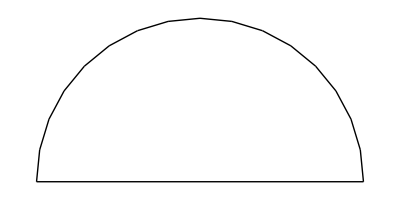

```mathematica
i=OpenCascadeShape[Disk[{0,0},1,{0,π}]];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[i];
ElementMeshProjection[bmesh,{#1,#2}&]["Wireframe"]
```

The boundary mesh refinement works in the standard way. This is described in more detail in the section Surface mesh generation.

Create a half disk, generate a refined boundary mesh and project the mesh to 2D.

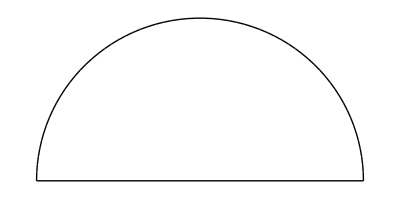

```mathematica
i=OpenCascadeShape[Disk[{0,0},1,{0,π}]];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[i,"ShapeSurfaceMeshOptions"->{"AngularDeflection"->0.1}];
ElementMeshProjection[bmesh,{#1,#2}&]["Wireframe"]
```

Note that now the boundary representation is less jagged.

#### Disk

Create a 2D Disk in OpenCascade.

```mathematica
i=OpenCascadeShape[Disk[{0,0},1,{0,π}]]
```

OpenCascadeShapeExpression[322]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### FilledCurve

FilledCurve is not  a region primitive. The main reason this graphics operation is partially supported in OpenCascadeLink is that in current versions of Mathematica there is no way to create a 2D region by connecting 1D segments that are embedded in 2D.

Create a boundary curve of 1D segments embedded in 2D.

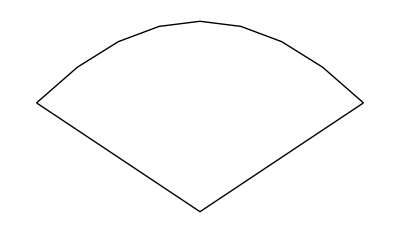

```mathematica
curves={BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]};
Graphics[curves]
```

For graphics FilledCurve can be used to mean the region that is enclosed by the curve.

Create 2D FilledCurve.

```mathematica
fc=FilledCurve[curves];
Graphics[fc]
```

-Graphics-

Create the 2D FilledCurve in OpenCascade.

```mathematica
i=OpenCascadeShape[fc]
```

OpenCascadeShapeExpression[310]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Create and visualize the boundary surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

The way OpenCascadeLink supports FilledCurce, and JoinedCurve for that matter, is a bit different from what they support in Graphics. For example, a Circle, can not be used as a segment in Graphics but it can be used in OpenCascadeLink.

Create a filled curve with a a Circle segment.

```mathematica
fc=FilledCurve[{Line[{{-1,0},{1,0}}],Circle[{0,0},1,{0,π}]}]
```

FilledCurve[{Line[{{-1,0},{1,0}}],Circle[{0,0},1,{0,π}]}]

Visualize the graphics filled curve with a helper function.

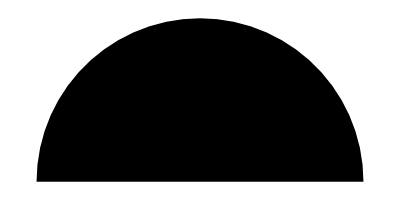

```mathematica
Graphics[fc/.Circle[data__]:>Sequence@@MeshPrimitives[DiscretizeRegion[Circle[data]], 1]]
```

Create the OpenCascade shape.

```mathematica
i=OpenCascadeShape[fc]
```

OpenCascadeShapeExpression[314]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Create and visualize the boundary surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

In the OpenCascadeLink implementation FilledCuve and JoindCurve must not have missing segments.

Create a filled curve where the segments are not connected.

```mathematica
fc=FilledCurve[{BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{0,-2/3},{-1,0}}]}]
```

FilledCurve[{BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{0,-2/3},{-1,0}}]}]

The conversion to OpenCascade will fail.

```mathematica
i=OpenCascadeShape[fc]
```

FilledCurve::discon: The last coordinate of segment BezierCurve[{{-1,0},{0,1},{1,0}}] is not connected to the first coordinate of segment Line[{{0,-2/3},{-1,0}}].

$Failed

```mathematica
(* BSplineCurve is not implented yet *)
fc=FilledCurve[{BSplineCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]}];
i=OpenCascadeShape[fc]
```

OpenCascadeShape[FilledCurve[{BSplineCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]}]]

JoinedCurve and FilledCurve options are currently not supported.

#### Parallelogram/Parallelepiped

Create a 2D Parallelogram in OpenCascade.

```mathematica
i=OpenCascadeShape[Parallelogram[]]
```

OpenCascadeShapeExpression[10]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### Polygon

Create a 2D Polygon in OpenCascade.

```mathematica
i=OpenCascadeShape[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]]
```

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### Rectangle

Create a 2D Rectangle in OpenCascade.

```mathematica
i=OpenCascadeShape[Rectangle[]]
```

OpenCascadeShapeExpression[13]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### RegularPolygon

Create a 2D RegularPolygon in OpenCascade.

```mathematica
i=OpenCascadeShape[RegularPolygon[{1,2},{1/2,0},6]]
```

OpenCascadeShapeExpression[2]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### Triangle

Create a 2D Triangle in OpenCascade.

```mathematica
i=OpenCascadeShape[Triangle[{{1,0},{0,Sqrt[3]},{-1,0}}]]
```

OpenCascadeShapeExpression[3]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Face

Visualize the surface mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i]["Wireframe"]
```

-Graphics3D-

#### Example

In this example we show how 2D graphics primitives can be used for creating a boundary element mesh. We would like to create a multi material region with a cutout described by a Bezier curve.

Create graphics primitives.

```mathematica
angle=2π/16;
r1=0.01;
r2=0.02;
offset=1/1000;
faces=Disk[{0,0},#,{0,angle}]&/@{r1,r1+offset,r2};
cut=FilledCurve[{BezierCurve[{{1/50,3/500},{2/500,0},{1/50,-3/500}}],Line[{{1/50,-3/500},{1/50,3/500}}]}];
```

Visualize the graphics primitives with an empty FaceForm and a black EdgeForm.

```mathematica
Graphics[{Directive[FaceForm[],EdgeForm[Black]],faces,cut},PlotRange->{{0,r2},All}]
```

-Graphics-

Create a union of the Disk faces.

```mathematica
ofs=OpenCascadeShape/@faces;
f1=OpenCascadeShapeUnion[ofs]
```

OpenCascadeShapeExpression[336]

Create the cut shape.

```mathematica
f2=OpenCascadeShape[cut]
```

OpenCascadeShapeExpression[340]

Compute the difference of the region with the cut.

```mathematica
f=OpenCascadeShapeDifference[f1,f2]
```

OpenCascadeShapeExpression[341]

Create a refined boundary surface mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[f,"ShapeSurfaceMeshOptions"->{"AngularDeflection"->0.1}];
bmesh["Wireframe"]
```

-Graphics3D-

Project the 3D surface mesh to a 2D boundary mesh.

```mathematica
bmesh2D=ElementMeshProjection[bmesh,{#1,#2}&]
```

ElementMesh[{{0.,0.0191757},{-3.52583×10^-16,0.00765367}},Automatic]

Visualize the boundary mesh.

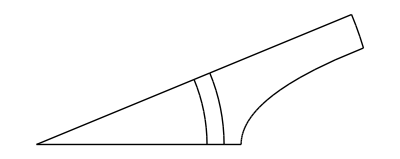

```mathematica
bmesh2D["Wireframe"]
```

Create and visualize a full 2D element mesh, with markers and a refined subregion.

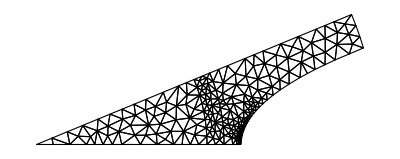

```mathematica
(mesh=ToElementMesh[bmesh2D,"RegionMarker"->{{{0.005,0.001},1},{{r1+offset/2,0.00005},2,0.0000001},{{0.013,0.004},3}}])["Wireframe"]
```

### Boundary 2D Primitives

Just like solid 2D graphics primitives can be converted, as explained in the section Solid 2D Primitives, we can also convert 2D edge or boundary graphics primitives such as Line and Circle.

The fundamental way this works is that 2D embedded objects are created in 3D in the x-y plane and the z-value is assumed 0. Since the shapes created are embedded in 3D OpenCascade operations like extrusion, Boolean operations etc can be applied in the same way as in the rest of the system.

#### Workflow

As a first step we illustrate a work flow for both scenarios. Let's start with creating a half circle and a line that closes the half circle.

Create a half disk.

```mathematica
i1=OpenCascadeShape[Circle[{0,0},1,{0,π}]]
i2=OpenCascadeShape[Line[{{-1,0},{1,0}}]]
```

OpenCascadeShapeExpression[1]

OpenCascadeShapeExpression[2]

Inspect the shape types.

```mathematica
OpenCascadeShapeType/@{i1,i2}
```

{Wire,Wire}

The next step is to connect the wires and create a face from them.

Connect wires and create a face.

```mathematica
wire=OpenCascadeShapeWire[{i1,i2}];
face=OpenCascadeShapeFace[wire]
```

OpenCascadeShapeExpression[9]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[face]
```

Face

The creation of a face from a set of wires can be done in one go.

Connect wires and create a face in one go.

```mathematica
face=OpenCascadeShapeFace[{i1,i2}]
```

OpenCascadeShapeExpression[10]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[face]
```

Face

Convert the OpenCascade shape into a boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face]
```

NDSolve`FEM`ElementMesh[{{-1.,1.},{0.,1.},{0.,0.}},Automatic]

Note that the boundary mesh generated is embedded in 3D and the z-extend is 0. The projection of this mesh to 3D will be shown in a minute.

Visualize the boundary mesh.

```mathematica
Show[
OpenCascadeAxis3D[],
bmesh["Wireframe"]]
```

-Graphics3D-

Back to the half circle and line object. This Object can be projected to any other position by using a transformation function. This works the same way as with other OpenCascade shapes.

Create a transformation function.

```mathematica
tf=RotationTransform[π/2,{1,0,0}]
```

TransformationFunction[(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)]

Apply the transformation function to the OpenCascade shape.

```mathematica
i2=OpenCascadeShapeTransformation[face,tf]
```

OpenCascadeShapeExpression[11]

Visualize the boundary mesh.

```mathematica
Show[
OpenCascadeAxis3D[],
OpenCascadeShapeSurfaceMeshToBoundaryMesh[i2]["Wireframe"]]
```

-Graphics3D-

To create a 2D boundary mesh the function ElementMeshProjection can be used.

Generate a boundary mesh and project the mesh to 2D.

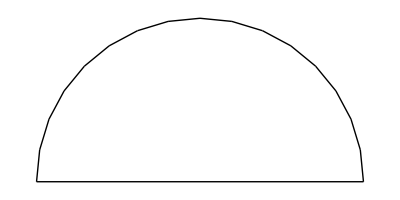

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face];
ElementMeshProjection[bmesh,{#1,#2}&]["Wireframe"]
```

The boundary mesh refinement works in the standard way. This is described in more detail in the section Surface mesh generation.

Generate a refined boundary mesh and project the mesh to 2D.

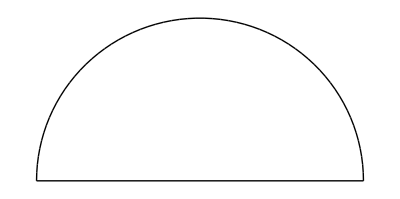

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face,"ShapeSurfaceMeshOptions"->{"AngularDeflection"->0.1}];
ElementMeshProjection[bmesh,{#1,#2}&]["Wireframe"]
```

Note that now the boundary representation is less jagged.

#### BezierCurve

Create a BezierCurve.

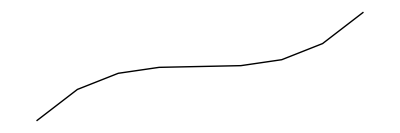

```mathematica
bc=BezierCurve[{{1,0},{2,1},{3,0},{4,1}}];
Graphics[bc]
```

Convert the curve to an OpenCacade shape.

```mathematica
i=OpenCascadeShape[bc]
```

OpenCascadeShapeExpression[19]

Inspect the type of the shape.

```mathematica
OpenCascadeShapeType[i]
```

Edge

#### Circle

Create a Circle.

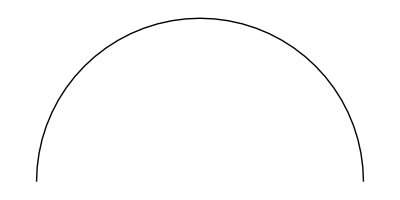

```mathematica
c=Circle[{0,0},1,{0,π}];
Graphics[c]
```

Convert the circle to an OpenCacade shape.

```mathematica
i=OpenCascadeShape[c]
```

OpenCascadeShapeExpression[20]

Inspect the type of the shape.

```mathematica
OpenCascadeShapeType[i]
```

Wire

#### JoinedCurve

JoinedCurve is not  a region primitive. The main reason this graphics operation is partially supported in OpenCascadeLink is that in current versions of Mathematica there is no way to create a connected region of 1D segments that are embedded in 2D.

Create a boundary curve of 1D segments embedded in 2D.

```mathematica
curves={BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]};
Graphics[curves]
```

-Graphics-

For graphics JoinedCurve can be used to mean the region that is enclosed by the curve.

Create JoinedCurve.

```mathematica
jc=JoinedCurve[curves];
Graphics[jc]
```

-Graphics-

Create the JoinedCurve in OpenCascade.

```mathematica
i=OpenCascadeShape[jc]
```

OpenCascadeShapeExpression[23]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Wire

The way OpenCascadeLink supports JoinedCurve, and FilledCurce for that matter, is a bit different from what they support in Graphics. For example, a Circle, can not be used as a segment in Graphics but it can be used in OpenCascadeLink.

Create a joined curve with a a Circle segment.

```mathematica
jc=JoinedCurve[{Line[{{-1,0},{1,0}}],Circle[{0,0},1,{0,π}]}]
```

JoinedCurve[{Line[{{-1,0},{1,0}}],Circle[{0,0},1,{0,π}]}]

Visualize the graphics filled curve with a helper function.

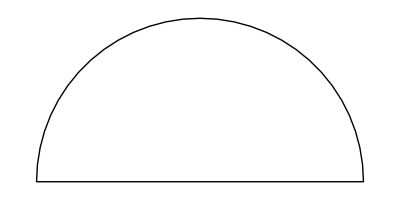

```mathematica
Graphics[jc/.Circle[data__]:>Sequence@@MeshPrimitives[DiscretizeRegion[Circle[data]], 1]]
```

Create the OpenCascade shape.

```mathematica
i=OpenCascadeShape[jc]
```

OpenCascadeShapeExpression[26]

Inspect the shape type.

```mathematica
OpenCascadeShapeType[i]
```

Wire

In the OpenCascadeLink implementation FilledCuve and JoindCurve must not have missing segments.

Create a joined curve where the segments are not connected.

```mathematica
jc=JoinedCurve[{BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{0,-2/3},{-1,0}}]}]
```

JoinedCurve[{BezierCurve[{{-1,0},{0,1},{1,0}}],Line[{{0,-2/3},{-1,0}}]}]

The conversion to OpenCascade will fail.

```mathematica
OpenCascadeShape[jc]
```

JoinedCurve::discon: The last coordinate of segment BezierCurve[{{-1,0},{0,1},{1,0}}] is not connected to the first coordinate of segment Line[{{0,-2/3},{-1,0}}].

$Failed

```mathematica
(* BSplineCurve is not implented yet *)
fc=FilledCurve[{BSplineCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]}];
i=OpenCascadeShape[fc]
```

OpenCascadeShape[FilledCurve[{BSplineCurve[{{-1,0},{0,1},{1,0}}],Line[{{1,0},{0,-2/3},{-1,0}}]}]]

JoinedCurve and FilledCurve options are currently not supported.

#### Line

Create a Line.

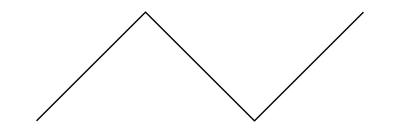

```mathematica
l=Line[{{1,0},{2,1},{3,0},{4,1}}];
Graphics[l]
```

Convert the circle to an OpenCacade shape.

```mathematica
i=OpenCascadeShape[l]
```

OpenCascadeShapeExpression[27]

Inspect the type of the shape.

```mathematica
OpenCascadeShapeType[i]
```

Wire

## Operations on OpenCascade objects

The following operations on OpenCascade objects are available:

Surface mesh generation

Part extraction

Geometric transformations

Sweeps

Boolean operations

Shape sewing

Internal boundary generation

Fillets

Chamfers

Lofting

Shelling

De-featuring

Shape simplification

Shape healing

### Surface mesh generation

Surfaces of OpenCascade objects can be meshed.

Generate an OpenCascade object.

```mathematica
shape=OpenCascadeShape[Cone[{{0,0,0},{0,0,1}},1]]
```

OpenCascadeShapeExpression[8247]

Generate a surface mesh.

```mathematica
OpenCascadeShapeSurfaceMesh[shape]
```

OpenCascadeShapeExpression[8247]

Extract and visualize the coordinates from the meshed shape.

```mathematica
c=OpenCascadeShapeSurfaceMeshCoordinates[shape];
Graphics3D[Point[c]]
```

-Graphics3D-

Extract and visualize the surface elements from the meshed shape.

```mathematica
ele=OpenCascadeShapeSurfaceMeshElements[shape];
Graphics3D[GraphicsComplex[c,Triangle[ele]]]
```

-Graphics3D-

OpenCascadeShapeSurfaceMesh has the following options:

```mathematica
Options[OpenCascadeShapeSurfaceMesh]
```

{AngularDeflection→Automatic,ComputeInParallel→Automatic,LinearDeflection→Automatic,Rediscretization→Automatic,RelativeDeflection→Automatic}

"AngularDeflection" and "LinearDeflection" specify the maximum amount a segment may deviate from the true surface. The concepts are best explained with the following illustration.

```mathematica
Rotate[Show[
Plot[Sin[x/2],{x,0,4π},Axes->None,AspectRatio->Automatic],

,PlotRange->All,ImageSize->Large],0.05π]
```

-Graphics-

"AngularDeflection" specifies the maximum deflection angle α at the end nodes of a segment while "LinearDeflection" specifies the maximum deflection d to the true curve within a segment. The Automatic default for the "AngularDeflection" is set to 0.5 degrees and the Automatic default for the "LinearDeflection" is set to 0.01 units of the relative size of the shape. For more information please consult the OpenCascade Documentation.

"ComputeInParallel" specifies if the surface discretization should be performed on multiple CPU cores. The Automatic default is set to False.

"RelativeDeflection" specifies if the deflection is relative or absolute to the size of the geometry. The Automatic default is set to True.

"Rediscretization" specifies if one of the input shapes already as a discretization attached to it if that discretization is to be reused. The Automatic default is set to False. This functionality is useful to have different levels of discretization on different parts in a multi material object. An example is given below in the section Internal boundaries refinement by sewing.

To make working with OpenCascade and the finite element method easier a function to mesh the surface and return a boundary ElementMesh is provided.

Extract a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,1.}},Automatic]

Visualize the boundary ElementMesh extracted from the OpenCascade shape.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Note that sub-surfaces have appropriate boundary markers.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->{FaceForm[Green],FaceForm[Red]}]]
```

-Graphics3D-

Create and visualize a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

OpenCascadeShapeSurfaceMeshToBoundaryMesh has the following options:

```mathematica
Options[OpenCascadeShapeSurfaceMeshToBoundaryMesh]
```

{ElementMeshOptions→Automatic,MarkerMethod→Automatic,ShapeSurfaceMeshOptions→Automatic}

All options that are relevant for the ElementMesh generation can be specified via "ElementMeshOptions" and options relevant for OpenCascadeShapeSurfaceMesh can be specified via "ShapeSurfaceMeshOptions".

The "MarkerMethod" option allows to specify if markers should be added and how they should be computed. The default is to use "OpenCascade". Other options are "ElementMesh" and None to switch off markers entirely. Using "ElementMesh" as a "MarkerMethod" option can be useful if the generated surface consists of many single surface elements. In that case the "OpenCascade" method would attribute each element a unique marker which may be undesirable. With the method "ElementMesh", however, the markers are added based on their face normals and if those deviate by a certain amount. The ToBoundaryMesh reference page has more information on this topic.

Extract a boundary ElementMesh from the OpenCascade shape with a refined surface mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape,"ShapeSurfaceMeshOptions"->{"LinearDeflection"->0.001}]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,1.}},Automatic]

Visualize the boundary ElementMesh extracted from the OpenCascade shape.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

### Part extraction

Create a shape.

```mathematica
shape=OpenCascadeShape[Cone[]]
```

OpenCascadeShapeExpression[8248]

Extract the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

2

Extract the faces.

```mathematica
faces=OpenCascadeShapeFaces[shape]
```

{OpenCascadeShapeExpression[8249],OpenCascadeShapeExpression[8250]}

Extract the type.

```mathematica
OpenCascadeShapeType/@faces
```

{Face,Face}

Generate a boundary mesh from one of the faces.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[faces[[1]]]["Wireframe"]
```

-Graphics3D-

Extract the number of vertices.

```mathematica
OpenCascadeShapeNumberOfVertices[shape]
```

10

Extract the vertices.

```mathematica
vertices=OpenCascadeShapeVertices[shape]
```

{OpenCascadeShapeExpression[8251],OpenCascadeShapeExpression[8252],OpenCascadeShapeExpression[8253],OpenCascadeShapeExpression[8254],OpenCascadeShapeExpression[8255],OpenCascadeShapeExpression[8256],OpenCascadeShapeExpression[8257],OpenCascadeShapeExpression[8258],OpenCascadeShapeExpression[8259],OpenCascadeShapeExpression[8260]}

Extract the type.

```mathematica
OpenCascadeShapeType/@vertices
```

{Vertex,Vertex,Vertex,Vertex,Vertex,Vertex,Vertex,Vertex,Vertex,Vertex}

### Geometric transformations

Create a shape.

```mathematica
shape=OpenCascadeShape[Cone[]]
```

OpenCascadeShapeExpression[8261]

Rotate the shape.

```mathematica
rshape=OpenCascadeShapeTransformation[shape,RotationTransform[10°,{0,1,0}]]
```

OpenCascadeShapeExpression[8262]

Extract a boundary ElementMesh from the OpenCascade shape.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[rshape]
```

ElementMesh[{{-1.1534,0.81116},{-0.998717,0.998717},{-1.15846,0.984808}},Automatic]

Visualize the boundary ElementMesh and the shape rotated in the Wolfram language.

```mathematica
Show[bmesh["Wireframe"],Graphics3D[TransformedRegion[Cone[],RotationTransform[10°,{0,1,0}]]]]
```

-Graphics3D-

As an alternative, the TransformationFunction can directly be applied during the creation of the OpenCascade shape by making use of a TransformedRegion.

Create a rotated shape.

```mathematica
rshape=OpenCascadeShape[TransformedRegion[Cone[],RotationTransform[20°,{0,1,1}]]]
```

OpenCascadeShapeExpression[8263]

Extract and visualize the boundary ElementMesh and the shape rotated in the Wolfram language.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[rshape];Show[bmesh["Wireframe"],Graphics3D[TransformedRegion[Cone[],RotationTransform[20°,{0,1,1}]]]]
```

-Graphics3D-

To mirror a shape ReflectionTransform can be used.

Create a mirrored shape.

```mathematica
rt=ReflectionTransform[{0,0,1},{0,0,1.1}];
rshape=OpenCascadeShape[TransformedRegion[Cone[],rt]]
```

OpenCascadeShapeExpression[8264]

Extract and visualize the boundary ElementMesh and the shape rotated in the Wolfram language.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[rshape];Show[bmesh["Wireframe"],Graphics3D[Cone[]]
,Graphics3D[GeometricTransformation[{Opacity[.85],Red,Cone[]},rt]]
]
```

-Graphics3D-

### Sweeps

#### RotationalSweeps

OpenCascade can perform rotational sweeps. For this a surface is rotated around an axis. The rotation can be less than a full rotation.

Create a polygon face in OpenCascade.

```mathematica
pp=Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}];
shape=OpenCascadeShape[pp]
```

OpenCascadeShapeExpression[8265]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Face

Specify a rotation axis and the amount of the rotation.

```mathematica
axis={{2,0,0},{2,1,0}};
sweep=OpenCascadeShapeRotationalSweep[shape, axis,-3π/2]
```

OpenCascadeShapeExpression[8266]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sweep]
```

Solid

Extract and visualize the boundary mesh, the rotation axis of rotation and the polygon face.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sweep];
Show[Graphics3D[{{Red,pp},{Blue,Thick,Arrow[axis]}}],bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{0.,4.},{0.,1.},{-2.,2.}},{TetrahedronElement[<6879>]}]

OpenCascade can also perform rotational sweeps on wire objects.

Create a Line primitive in OpenCascade.

```mathematica
ll=Line[{{0,1,0},{1,1,0},{1.5,2,0},{2,2,0}}];
wire=OpenCascadeShape[ll]
```

OpenCascadeShapeExpression[8267]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

Specify a rotation axis and the amount of the rotation.

```mathematica
axis={{0,0,0},{1,0,0}};
sweep=OpenCascadeShapeRotationalSweep[wire,axis]
```

OpenCascadeShapeExpression[8268]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sweep]
```

Shell

Extract and visualize the boundary mesh, the rotation axis of rotation and the Line edge.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sweep];
Show[Graphics3D[{{Red,Thickness[0.02],ll},{Blue,Thick,Arrow[axis]}}],bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

Rotational sweeps can not be performed on Solid or CompoundSolid OpenCascade shape types.

OpenCascade can also perform rotational sweeps on edge objects.

Visualize a Circle in 3D.

```mathematica
gr={Red,Thickness[0.02],Circle3D[{{0,0,1},{0,-1,0}},1/2,{π,2π}]};
Show[Graphics3D[gr],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Create a OpenCascadeCricle primitive in OpenCascade.

```mathematica
wire=OpenCascadeShape[OpenCascadeCircle[{{0,0,1},{0,-1,0}},1/2,{π,2π}]]
```

OpenCascadeShapeExpression[8269]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

Specify a rotation axis and the amount of the rotation.

```mathematica
axis={{0,0,0},{1,0,0}};
sweep=OpenCascadeShapeRotationalSweep[wire, axis,3π/2]
```

OpenCascadeShapeExpression[8270]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sweep]
```

Shell

Extract and visualize the boundary mesh, the rotation axis of rotation and the Line edge.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sweep];
Show[Graphics3D[{gr,{Blue,Thick,Arrow[axis]}}],bmesh["Wireframe"],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Rotational sweeps can not be performed on Solid or CompoundSolid OpenCascade shape types.

#### LinearSweeps

For a linear sweep of a surface a starting point on the surface and destination point are given and the surface is swept to the destination point.

Create a polygon face in OpenCascade.

```mathematica
pp=Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}];
shape=OpenCascadeShape[pp]
```

OpenCascadeShapeExpression[8271]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Face

Sweep the surface from {1/2,1/2,0} to {1,1,1}.

```mathematica
sweep=OpenCascadeShapeLinearSweep[shape, {{1/2,1/2,0},{1,1,1}}]
```

OpenCascadeShapeExpression[8272]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sweep]
```

Solid

Extract and visualize the boundary mesh, the rotation axis of rotation and the polygon face.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sweep];
Show[Graphics3D[{{Red,pp},{Blue,Thick,Arrow[{{1/2,1/2,0},{1,1,1}}]}}],bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{0.,1.5},{0.,1.5},{0.,1.}},{TetrahedronElement[<6648>]}]

OpenCascade can also perform linear sweeps on wire objects.

Create a Line primitive in OpenCascade.

```mathematica
ll=Line[{{0,1,0},{1,1,0},{1.5,2,0},{2,2,0}}];
wire=OpenCascadeShape[ll]
```

OpenCascadeShapeExpression[8273]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[wire]
```

Wire

Sweep the surface from {1/2,1/2,0} to {1,1,1}.

```mathematica
axis={{1/2,1/2,0},{1,1,1}};
sweep=OpenCascadeShapeLinearSweep[wire, axis]
```

OpenCascadeShapeExpression[8274]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sweep]
```

Shell

Extract and visualize the boundary mesh, the rotation axis of rotation and the Line edge.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sweep];
Show[Graphics3D[{{Red,Thickness[0.02],ll},{Blue,Thick,Arrow[axis]}}],bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

Linear sweeps can not be performed on Solid or CompundSolid OpenCascade shape types.

### Boolean Operations

Some restrictions in computing Boolean operations are detailed in the Boolean possible issues section and the Boolean operations on solids section.

Boolean operations will always return compound objects.

#### Difference

Compute geometric differences of shapes.

Generate two Ball shapes.

```mathematica
b1=Ball[];
b2=Ball[{1,-1/2,0},1/2];
shape1=OpenCascadeShape[b1];
shape2=OpenCascadeShape[b2];
```

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ {shape1,shape2}
```

{Solid,Solid}

Compute the geometric difference between the two shapes

```mathematica
difference=OpenCascadeShapeDifference[shape1,shape2]
```

OpenCascadeShapeExpression[8277]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[difference]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[difference];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Generate a Prism and a Ball Graphics3D primitive.

```mathematica
p1=Prism[{{1,0,1},{0,0,0},{2,0,0},{1,2,1},{0,2,0},{2,2,0}}];
b1=Ball[{1,0,-1/10}];
```

Visualize the scene.

```mathematica
Graphics3D[{p1,b1}]
```

-Graphics3D-

Generate the OpenCascade shape instances.

```mathematica
shape1=OpenCascadeShape[p1];
shape2=OpenCascadeShape[b1];
```

Compute the geometric difference.

```mathematica
difference=OpenCascadeShapeDifference[shape1,shape2]
```

OpenCascadeShapeExpression[8280]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[difference]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[difference];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9821364383651212, 0.5110172702414657, 0.6498306075283933],RGBColor[0.6308358608594066, 0.5593312522653415, 0.9997714945145527],RGBColor[0.2783138319842018, 0.7738937595224964, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.6091400306115944, 0.9924863936620901, 0.45551440491106865],RGBColor[0.9866205624332851, 0.9581441900989159, 0.4023413079796949],RGBColor[1., 0.564994369252848, 0.1298465177047566]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a SphericalShell and a Cylinder shape.

```mathematica
shape1=OpenCascadeShape[SphericalShell[]];
shape2=OpenCascadeShape[Cylinder[{{0,0,0},{1,-2,3}},1/2]];
```

Compute the geometric difference of the shapes

```mathematica
difference=OpenCascadeShapeDifference[shape1,shape2]
```

OpenCascadeShapeExpression[8286]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[difference];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.14287214708202123, 0.7165497398815136, 1.],RGBColor[0.9729188047180777, 0.9391259962046635, 0.201748879675973]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a Polyhedron and a Ball primitive in OpenCascade.

```mathematica
polyhedron=Polyhedron[…];
shape1=OpenCascadeShape[polyhedron]
shape2=OpenCascadeShape[Ball[{1,0,0},1/2]]
```

OpenCascadeShapeExpression[8308]

OpenCascadeShapeExpression[8309]

Compute the geometric difference of the shapes

```mathematica
difference=OpenCascadeShapeDifference[shape1,shape2]
```

OpenCascadeShapeExpression[8310]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[difference]
```

ElementMesh[{{-1.37638,1.28489},{-1.30902,1.30902},{-1.11352,1.11352}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9398277357012335, 0.294377068348925, 0.4107881682486557],RGBColor[0.977435471402467, 0.4869461366978501, 0.6232703364973113],RGBColor[0.45641128340454246, 0.3644465670061772, 0.9999446044160554],RGBColor[0.5959509453684337, 0.5203543152135086, 0.9998061164948533],RGBColor[0.7354906073323251, 0.67626206342084, 0.9996676285736512],RGBColor[0.20660941056540044, 0.7435351608890349, 1.],RGBColor[0.39782120101553753, 0.8244914239115988, 1.],RGBColor[0.5890329914656748, 0.9054476869341627, 1.],RGBColor[0.32302624809866454, 0.9734583801361795, 0.19560507992137266],RGBColor[0.4990962681066214, 0.9851679269213554, 0.35554927991503177],RGBColor[0.6751662881145782, 0.9968774737065311, 0.515493479908691],RGBColor[0.9793666907017047, 0.9480757345078412, 0.2961453165247835],RGBColor[0.9890385196771452, 0.9615003419626076, 0.4377399717979986],RGBColor[0.9987103486525858, 0.974924949417374, 0.5793346270712141],RGBColor[1., 0.5758624651791511, 0.15168984019271203],RGBColor[1., 0.6628072325895755, 0.32643642009635604]}

Visualize a cross section through the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors,PlotRange->{{-1.5,1.5},{0,1.5},{-1.2,1.2}}]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Union

Compute geometric unions of shapes.

Generate two Ball shapes.

```mathematica
b1=Ball[];
b2=Ball[{1,-1/2,0},1/2];
shape1=OpenCascadeShape[b1];
shape2=OpenCascadeShape[b2];
```

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ {shape1,shape2}
```

{Solid,Solid}

Compute the geometric union.

```mathematica
union=OpenCascadeShapeUnion[shape1,shape2]
```

OpenCascadeShapeExpression[8313]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[union]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a Ball and a Hexahedron shape.

```mathematica
shape1=OpenCascadeShape[Ball[{0,0,1},1/2]];
shape2=OpenCascadeShape[Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}]];
```

Compute the geometric union of the shapes

```mathematica
union=OpenCascadeShapeUnion[shape1,shape2]
```

OpenCascadeShapeExpression[8322]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9935530724172814, 0.5694757374188179, 0.7143341228895923],RGBColor[0.715556369908912, 0.6539895279626498, 0.9996874125623944],RGBColor[0.45245314114414814, 0.8476217847751885, 1.],RGBColor[0.4487905481043478, 0.9818223421255908, 0.3098509370597005],RGBColor[0.9807483805553391, 0.9499935355728077, 0.316373124420957],RGBColor[1., 0.5386004220032548, 0.07679844880543597]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a Ball and a Pyramid shape.

```mathematica
shape1=OpenCascadeShape[Ball[{0,0,1},1/2]];
shape2=OpenCascadeShape[Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}-1]];
```

Compute the geometric union of the shapes

```mathematica
union=OpenCascadeShapeUnion[shape1,shape2]
```

OpenCascadeShapeExpression[8330]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.43315467307722716, 0.3384619423049553, 0.9999676857362557],RGBColor[0.14287214708202123, 0.7165497398815136, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.9729188047180777, 0.9391259962046635, 0.201748879675973],RGBColor[1., 0.5034084923371307, 0.0060676902730088965]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a SphericalShell and a Cylinder shape.

```mathematica
shape1=OpenCascadeShape[SphericalShell[]];
shape2=OpenCascadeShape[Cylinder[{{0,0,0},{1,2,3}},1/2]];
```

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ {shape1,shape2}
```

{Solid,Solid}

Compute the geometric union of the shapes

```mathematica
union=OpenCascadeShapeUnion[shape1,shape2]
```

OpenCascadeShapeExpression[8336]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[union]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
```

Visualize the boundary ElementMesh..

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

#### Intersection

Compute geometric intersection of shapes.

Generate two Ball shapes.

```mathematica
b1=Ball[];
b2=Ball[{1,-1/2,0},1/2];
shape1=OpenCascadeShape[b1];
shape2=OpenCascadeShape[b2];
```

Compute the geometric union.

```mathematica
intersection=OpenCascadeShapeIntersection[shape1,shape2]
```

OpenCascadeShapeExpression[8339]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a Ball and a Hexahedron shape.

```mathematica
shape1=OpenCascadeShape[Ball[{0,0,1},1/2]];
shape2=OpenCascadeShape[Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}]];
```

Compute the geometric intersection of the shapes

```mathematica
intersection=OpenCascadeShapeIntersection[shape1,shape2]
```

OpenCascadeShapeExpression[8348]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.6308358608594066, 0.5593312522653415, 0.9997714945145527],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.9866205624332851, 0.9581441900989159, 0.4023413079796949]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a Ball and a Pyramid shape.

```mathematica
shape1=OpenCascadeShape[Ball[{0,0,1},1/2]];
shape2=OpenCascadeShape[Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}-1]];
```

Compute the geometric intersection of the shapes

```mathematica
intersection=OpenCascadeShapeIntersection[shape1,shape2]
```

OpenCascadeShapeExpression[8356]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.512227148190099, 0.42680966628910977, 0.9998892092475745],RGBColor[0.35957884292551023, 0.8083001713070861, 1.],RGBColor[0.5343102721082127, 0.9875098362783905, 0.3875381199137635],RGBColor[0.9948416170624096, 0.9695551064354674, 0.5226967649619281]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Create a SphericalShell and a Cylinder shape.

```mathematica
shape1=OpenCascadeShape[SphericalShell[]];
shape2=OpenCascadeShape[Cylinder[{{0,0,0},{1,2,3}},1/2]];
```

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ {shape1,shape2}
```

{Solid,Solid}

Compute the geometric intersection of the shapes.

```mathematica
intersection=OpenCascadeShapeIntersection[shape1,shape2]
```

OpenCascadeShapeExpression[8362]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[intersection]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection];
```

Visualize the boundary ElementMesh..

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Intersections can also be generated from lower dimensional region objects.

Create a Cone and a Polygon shape.

```mathematica
c1=Cone[{{0,0,0},{0,0,1}},1];
shape1=OpenCascadeShape[c1];
shape2=OpenCascadeShape[Polygon[{{-2,0,-2},{2,0,-2},{2,0,2},{-2,0,2}}]];
```

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ {shape1,shape2}
```

{Solid,Face}

Compute the geometric intersection of the shapes.

```mathematica
intersection=OpenCascadeShapeIntersection[shape1,shape2]
```

OpenCascadeShapeExpression[8365]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[intersection]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection];
```

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Visualize the boundary ElementMesh in the Cone.

```mathematica
Show[bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[Green],EdgeForm[Red]]]],Graphics3D[{Opacity[0.15],c1}],Boxed->False]
```

-Graphics3D-

#### Simplifications of Boolean operations

In some cases the surfaces resulting from Boolean operations can be simplified.

A default union of two cuboids:

```mathematica
c1=Cuboid[{0,0,0},{1,1,1}];
c2=Cuboid[{1/2,0,0},{2,2,2}];
u1=OpenCascadeShapeUnion[OpenCascadeShape/@{c1,c2}];
OpenCascadeShapeSurfaceMeshToBoundaryMesh[u1]["Wireframe"]
```

-Graphics3D-

A union of two cuboids with surface simplification:

```mathematica
c1=Cuboid[{0,0,0},{1,1,1}];
c2=Cuboid[{1/2,0,0},{2,2,2}];
u1=OpenCascadeShapeUnion[OpenCascadeShape/@{c1,c2},"SimplifyResult"->True];
OpenCascadeShapeSurfaceMeshToBoundaryMesh[u1]["Wireframe"]
```

-Graphics3D-

#### BooleanRegion

The OpenCascadeLink provides functionality to directly work with BooleanRegion objects.

Generate a BooleanRegion shape.

```mathematica
shape=OpenCascadeShapeBooleanRegion[BooleanRegion[Or,{Cuboid[],Ball[{1,1,1}]}]]
```

OpenCascadeShapeExpression[8374]

As a convenience it is also possible to use OpenCascadeShape for BooleanRegion objects directly.

Alternative to generate a BooleanRegion shape.

```mathematica
shape=OpenCascadeShape[BooleanRegion[Or,{Cuboid[],Ball[{1,1,1}]}]]
```

OpenCascadeShapeExpression[8377]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9935530724172814, 0.5694757374188179, 0.7143341228895923],RGBColor[0.715556369908912, 0.6539895279626498, 0.9996874125623944],RGBColor[0.45245314114414814, 0.8476217847751885, 1.],RGBColor[0.4487905481043478, 0.9818223421255908, 0.3098509370597005],RGBColor[0.9807483805553391, 0.9499935355728077, 0.316373124420957],RGBColor[1., 0.5386004220032548, 0.07679844880543597]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Generate a BooleanRegion shape.

```mathematica
shape=OpenCascadeShape[BooleanRegion[And,{Cuboid[],Ball[{1,1,1}]}]]
```

OpenCascadeShapeExpression[8380]

Extract and visualize the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"]
```

-Graphics3D-

Generate a BooleanRegion shape.

```mathematica
shape=OpenCascadeShape[BooleanRegion[¬#2∧#1&,{Cuboid[],Ball[{1,1,1}]}]]
```

OpenCascadeShapeExpression[8383]

Extract and visualize the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"]
```

-Graphics3D-

#### Boolean operations on solids

OpenCascade handles Boolean operations in a slightly different manner than the Wolfram Language Boolean operators RegionUnion, RegionIntersection and RegionDifference. It's illustrative to walk through several examples.

##### Solids overlapping

Create two overlapping cubes.

```mathematica
gr1=Graphics3D[{{Opacity[0.5],c1=Cuboid[],c2=Cuboid[{1/4,1/4,1/4}]}},Boxed->False]
```

-Graphics3D-

Setup the shapes.

```mathematica
s1=OpenCascadeShape[c1];
s2=OpenCascadeShape[c2];
```

Intersection

Compute the intersection.

```mathematica
shape=OpenCascadeShapeIntersection[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Union

Compute the union.

```mathematica
shape=OpenCascadeShapeUnion[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Difference

Compute the first difference.

```mathematica
shape=OpenCascadeShapeDifference[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Compute the second difference.

```mathematica
shape=OpenCascadeShapeDifference[s2,s1];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

##### Solids touching at a face

Create two touching cubes.

```mathematica
gr1=Graphics3D[{{Opacity[0.5],c1=Cuboid[],c2=Cuboid[{1,1/2,1/2}]}},Boxed->False]
```

-Graphics3D-

Setup the shapes.

```mathematica
s1=OpenCascadeShape[c1];
s2=OpenCascadeShape[c2];
```

Intersection

Compute the intersection.

```mathematica
shape=OpenCascadeShapeIntersection[s1,s2];
```

The lowest dimensional object that can be returned from an OpenCascase Boolean operation is that of the minimal dimension of any argument given to the Boolean operation. For example, a Boolean operation of two OpenCascade solids can not return an OpenCascade face object.

Extract the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

0

Since there are no solids and no faces the conversion to a boundary element mesh will fail.

Converting a shape with no faces or solids will fail.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

$Failed

Union

Compute the union.

```mathematica
shape=OpenCascadeShapeUnion[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the resulting full mesh will be open at the touching faces.

Visualize the full mesh and note that the union of the solids is open at the touching faces.

```mathematica
ToElementMesh[OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape],MaxCellMeasure->0.005]["Wireframe"]
```

-Graphics3D-

Difference

Compute the first difference.

```mathematica
shape=OpenCascadeShapeDifference[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the resulting solid has it's surface split according to the shape of the touching object.

Visualize the boundary mesh and it's split surface.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]
```

-Graphics3D-

Compute the second difference.

```mathematica
shape=OpenCascadeShapeDifference[s2,s1];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the resulting solid has it's surface split according to the shape of the touching object.

##### Solids touching at an edge

Create two touching cubes that touch at an edge.

```mathematica
gr1=Graphics3D[{{Opacity[0.5],c1=Cuboid[],c2=Cuboid[{1,1,1/2}]}},Boxed->False]
```

-Graphics3D-

Setup the shapes.

```mathematica
s1=OpenCascadeShape[c1];
s2=OpenCascadeShape[c2];
```

Intersection

Compute the intersection.

```mathematica
shape=OpenCascadeShapeIntersection[s1,s2];
```

The lowest dimensional object that can be returned from an OpenCascase Boolean operation is that of the minimal dimension of any argument given to the Boolean operation. For example, a Boolean operation of two OpenCascade solids can not return an OpenCascade face object.

Extract the number of edges.

```mathematica
OpenCascadeShapeNumberOfEdges[shape]
```

0

Union

Compute the union.

```mathematica
shape=OpenCascadeShapeUnion[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the edge of resulting full mesh will be split at the touching edges.

Visualize the full mesh and note that the union of the solids is split at the touching edges.

```mathematica
ToElementMesh[OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape],MaxCellMeasure->Infinity]["Wireframe"]
```

-Graphics3D-

Difference

Compute the first difference.

```mathematica
shape=OpenCascadeShapeDifference[s1,s2];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the edge of resulting boundary mesh will be split at the touching edges.

Visualize the boundary mesh and it's split surface.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]
```

-Graphics3D-

Compute the second difference.

```mathematica
shape=OpenCascadeShapeDifference[s2,s1];
```

Visualize the Boolean operation.

```mathematica
Show[gr1,OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"["MeshElementStyle"->{FaceForm[Blue]}]]]
```

-Graphics3D-

Note that the edge of resulting boundary mesh will be split at the touching edges.

### Sewing

Surfaces that share edges can be sewn together.

Generate a list of polygons.

```mathematica
data={Polygon[{{0,1,0},{1,0,0},{0,0,0}}],Polygon[{{0,0,2},{1,0,0},{0,0,0}}],Polygon[{{0,0,2},{0,1,0},{1,0,0}}],Polygon[{{0,0,2},{0,0,0},{0,1,0}}]};
```

Create the polygons in OpenCacade.

```mathematica
ocFaces=OpenCascadeShape[#]&/@data
```

{OpenCascadeShapeExpression[8402],OpenCascadeShapeExpression[8403],OpenCascadeShapeExpression[8404],OpenCascadeShapeExpression[8405]}

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType /@ocFaces
```

{Face,Face,Face,Face}

Sew the faces together.

```mathematica
sewenFaces=OpenCascadeShapeSewing[ocFaces]
```

OpenCascadeShapeExpression[8406]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sewenFaces]
```

Shell

A shell is a collection of faces. To create a solid either an option can be used during the sewing process or the function OpenCascadeShapeSolid can be used.

Sew the faces together.

```mathematica
sewenFaces=OpenCascadeShapeSewing[ocFaces,"BuildSolid"->True]
```

OpenCascadeShapeExpression[8407]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[sewenFaces]
```

Solid

Extract and visualize the boundary ElementMesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[sewenFaces]
bmesh["Wireframe"]
```

ElementMesh[{{0.,1.},{0.,1.},{0.,2.}},Automatic]

-Graphics3D-

Create and visualize a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Sewing of B-Spline surfaces with other objects is possible. However, nodes need to match.

Create a PolarPlot.

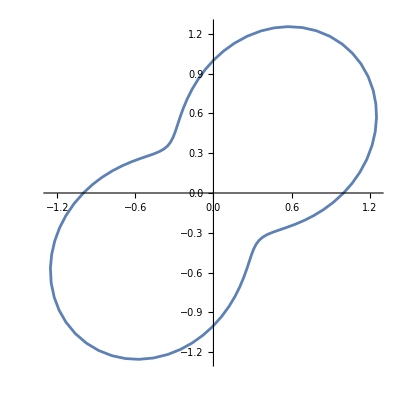

```mathematica
pp=PolarPlot[1+0.5 Sin[2 θ],{θ,0,2 π},MaxRecursion->1,PlotPoints->45]
```

Extract the coordinates from the PolarPlot.

```mathematica
coordinates=First[Cases[Normal[pp],Line[l_]:>l,∞]];
```

Make use of a function to parameterize the coordinates of the shape.

```mathematica
parametrizeCurve[pts_List,a:(_?NumericQ):1/2]:=FoldList[Plus,0,Normalize[(Norm/@Differences[pts])^a,Total]]/;MatrixQ[pts,NumericQ]
tvals=parametrizeCurve[coordinates,1];
```

Construct the BSplineSurface.

```mathematica
bottom = ArrayPad[coordinates,{{0,0},{0,1}},-1.];
top = ArrayPad[coordinates,{{0,0},{0,1}},2.];
knots = Join[{0.,0.},tvals[[2;;-2]],{1.,1.}];
bss = BSplineSurface[Transpose[{bottom,top}],SplineDegree→1,SplineKnots→{knots,{0,0,1,1}}];
```

Visualize the BSplineSurface and the top and bottom cap.

```mathematica
gr=Graphics3D[{EdgeForm[],Polygon[top],Polygon[bottom],bss},Boxed->False]
```

-Graphics3D-

Construct the surfaces in OpenCascade.

```mathematica
surface=OpenCascadeShape[bss];
p1=OpenCascadeShape[Polygon[top]];
p2=OpenCascadeShape[Polygon[bottom]];
```

Sew the surfaces together.

```mathematica
shape=OpenCascadeShapeSewing[{surface,p1,p2}]
```

OpenCascadeShapeExpression[8411]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Shell

Convert to a solid.

```mathematica
shape=OpenCascadeShapeSolid[shape];
OpenCascadeShapeType[shape]
```

Solid

Extract and visualize the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
Show[gr,bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{-1.25321,1.25327},{-1.25337,1.25332},{-1.,2.}},{TetrahedronElement[<15434>]}]

As a further example an Ellipsoid is created from 8 BSplineSurface patches.

Create and visualize an Ellipsoid.

```mathematica
center={0,1,-1/2};
sigma={{5,2,3},{2,3,2},{3,2,5}};
el=Ellipsoid[center,sigma];
gr=Graphics3D[el,Boxed->False]
```

-Graphics3D-

Compute the eigenvalues and eigenvectors of the Ellipsoid.

```mathematica
matrix=If[VectorQ[sigma],
DiagonalMatrix[sigma^2],
sigma];
{vals,vecs}=Eigensystem[N[matrix]];
```

Compute the TransformationFunction to map a unit Ball onto the Ellipsoid.

```mathematica
composition=Composition[TranslationTransform[center],AffineTransform[Transpose[vecs]],ScalingTransform[Sqrt[vals]]]
```

TransformationFunction[(-1.96325 | -1. | 0.381647 | 0.
-1.25149 | 2.13485×10^-15 | -1.1974 | 1.
-1.96325 | 1. | 0.381647 | -0.5
0. | 0. | 0. | 1.)]

Set up the control points for 8 B-Spline surfaces and generate the surfaces.

```mathematica
pts1={{{1,0,0},{1,1,0},{0,1,0}},
{{1,0,1},{1,1,1},{0,1,1}},
{{0,0,1},{0,0,1},{0,0,1}}};
pts2={{{0,1,0},{-1,1,0},{-1,0,0}},
{{0,1,1},{-1,1,1},{-1,0,1}},
{{0,0,1},{0,0,1},{0,0,1}}};
pts3={{{-1,0,0},{-1,-1,0},{0,-1,0}},
{{-1,0,1},{-1,-1,1},{0,-1,1}},
{{0,0,1},{0,0,1},{0,0,1}}};
pts4={{{0,-1,0},{1,-1,0},{1,0,0}},
{{0,-1,1},{1,-1,1},{1,0,1}},
{{0,0,1},{0,0,1},{0,0,1}}};
pts={pts1,pts2,pts3,pts4,-pts1,-pts2,-pts3,-pts4};
bsss=Table[BSplineSurface[composition/@d,SplineDegree->2,SplineKnots->{{0,0,0,1,1,1},{0,0,0,1,1,1}},SplineWeights->{{1,1/Sqrt[2],1},{1/Sqrt[2],1/2,1/Sqrt[2]},{1,1/Sqrt[2],1}}],{d,pts}];
```

Note, here the ordering of the control points pts is important. The orientation of the resulting surfaces can be fixed with OpenCascadeShapeFix as shown further down.

Convert the B-Spline surfaces into OpenCascade expressions.

```mathematica
bsurfs=OpenCascadeShape/@bsss
```

{OpenCascadeShapeExpression[8413],OpenCascadeShapeExpression[8414],OpenCascadeShapeExpression[8415],OpenCascadeShapeExpression[8416],OpenCascadeShapeExpression[8417],OpenCascadeShapeExpression[8418],OpenCascadeShapeExpression[8419],OpenCascadeShapeExpression[8420]}

Sew the surfaces together and make the shape a solid.

```mathematica
shape=OpenCascadeShapeSewing[bsurfs,"BuildSolid"->True]
```

OpenCascadeShapeExpression[8421]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Extract and visualize the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
Show[gr,bmesh["Wireframe"],Boxed->False]
```

-Graphics3D-

A possible issue is that OpenCascade is sensitive to the ordering of the surfaces given for sewing. This may be tricky to note as a displayed surface might look good but when, for example, Boolean operations are performed on the object unexpected results may happen.

Compute the Boolean union of a the ellipsoid and a cuboid.

```mathematica
cu=OpenCascadeShape[Cuboid[{0,0,0},{2,2,2}]];
union=OpenCascadeShapeUnion[cu,shape];
OpenCascadeShapeSurfaceMeshToBoundaryMesh[union]["Wireframe"]
```

-Graphics3D-

### Internal boundaries

OpenCascade offers several ways to include internal boundaries for creating geometric models with multiple materials.

#### Internal boundaries by union of faces

Forming the union of solids will leave the position of the over lap open.

Create two touching cubes that touch at an edge.

```mathematica
Graphics3D[{{Opacity[0.5],c1=Cuboid[{0,0,0},{0.5,1,1}],c2=Cuboid[{0.5,0,0},{1,1,2}]}},Boxed->False]
```

-Graphics3D-

Create the OpenCascade shapes.

```mathematica
shape1=OpenCascadeShape[c1];
shape2=OpenCascadeShape[c2];
```

Form the union and visualize the full mesh.

```mathematica
union = OpenCascadeShapeUnion [shape1, shape2];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
ToElementMesh[bmesh,MaxCellMeasure->0.01]["Wireframe"]
```

-Graphics3D-

Note that at the overlap where the two cuboids touched the union is not closed. This may be undesirable if one is working with a multiple material region. One option to close the face at the overlap is to compute the union of all faces of the solids.

Extract all faces from the solids and compute the union of the faces.

```mathematica
faces1=OpenCascadeShapeFaces[shape1];
faces2=OpenCascadeShapeFaces[shape2];
union=OpenCascadeShapeUnion[Flatten[{faces1,faces2}]]
```

OpenCascadeShapeExpression[8449]

Visualize the full mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
ToElementMesh[bmesh,MaxCellMeasure->0.01]["Wireframe"]
```

-Graphics3D-

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[union];
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

Note that now an interface exists between the two solids.

#### Internal boundaries by sewing

Shape sewing can also be used to generate shapes that have internal boundaries.

Generate two shapes.

```mathematica
shape1=OpenCascadeShape[Cuboid[{-2,-2,-2},{2,2,1/2}]];
shape2=OpenCascadeShape[Cylinder[]];
```

Compute the geometric union between the two shapes.

```mathematica
union=OpenCascadeShapeUnion [shape1,shape2]
```

OpenCascadeShapeExpression[8452]

Visualize the resulting union.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[union]["Wireframe"]
```

-Graphics3D-

Compute the geometric intersection between the two shapes.

```mathematica
intersection=OpenCascadeShapeIntersection [shape1,shape2]
```

OpenCascadeShapeExpression[8453]

Visualize the resulting intersection.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection]["Wireframe"]
```

-Graphics3D-

Note that computing the intersection returns a closed shape.

Sew the faces together.

```mathematica
shape=OpenCascadeShapeSewing[{union,intersection}]
```

OpenCascadeShapeExpression[8454]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
```

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9603410460837245, 0.39941474199379323, 0.5266875327479225],RGBColor[0.46909670721944163, 0.3786199986613892, 0.999932014605037],RGBColor[0.6847489120727281, 0.6195683367999922, 0.9997179878177247],RGBColor[0.2413751906472435, 0.758254481438592, 1.],RGBColor[0.53688432134291, 0.883368706109827, 1.],RGBColor[0.3710453444644708, 0.9766518928957729, 0.23922622537418864],RGBColor[0.6431535572040405, 0.9947484652001355, 0.48641271627348004],RGBColor[0.9828837194200467, 0.952957409945938, 0.3476342820786799],RGBColor[0.9978310914730003, 0.9737045305578498, 0.5664623856827402],RGBColor[1., 0.6153828140020712, 0.23112010378527748]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors,PlotRange->{All,{-1,2},All}]]
```

-Graphics3D-

Since the intersection of the two shapes is closed by sewing that closed shape into the union of the shapes we have three internal regions. One in the cylinder on top of the cuboid, one in the cylinder that is inside the cuboid and one in the remaining cuboid.

Generate a full mesh.

```mathematica
mesh=ToElementMesh[bmesh,"RegionMarker"->{{{-1,-1,-1},1},{{0,0,3/4},2},{{0,0,1/4},3}}]
```

ElementMesh[{{-2.,2.},{-2.,2.},{-2.,1.}},{TetrahedronElement[<13629>]}]

Check that all markers are present.

```mathematica
mesh["MeshElementMarkerUnion"]
```

{1,2,3}

Visualize the parts specified by the markers.

```mathematica
parts=Map[mesh["Wireframe"[ElementMarker==#[[1]],"MeshElement"->"MeshElements","ElementMeshDirective"->Directive[EdgeForm[],FaceForm[#[[2]]]]]]&,{{1,Gray},{2,Pink},{3,Orange}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Visualize a cross section through the mesh with markers highlighted.

```mathematica
Rasterize[Show[parts,PlotRange->{All,{-0.02,2},All}]]
```

-Graphics-

#### Internal boundaries refinement by sewing

Sometimes it is desirable to have different internal boundaries discretized at different resolutions. This can be achieved by discretizing the respective boundaries to a desired level and then sew them together.

Create symbolic regions:

```mathematica
cylinder=Cylinder[{{0,0,3.097},{0,0,3.097+6}},3];
cuboid1=Cuboid[{-10,-10,-10},{10,10,10}];
cuboid2=Cuboid[{-5,-5,-2},{5,5,2}];
```

Convert the symbolic regions to OpenCascade and sew them together:

```mathematica
cylinderShape=OpenCascadeShape[cylinder];
cuboid1Shape=OpenCascadeShape[cuboid1];
cuboid2Shape=OpenCascadeShape[cuboid2];
shape=OpenCascadeShapeSewing[{cylinderShape,cuboid1Shape,cuboid1Shape}]
```

OpenCascadeShapeExpression[8458]

Discretize the boundary and visualize the discretization:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape];
bmesh["Wireframe"]
```

-Graphics3D-

Now, what if you want to refine the inner cylinder and not the boundary of the cuboids? Changing the linear or angular deflection during on the sewn object is going to affect all boundaries. To still change the discretization of a single shape in the object it is possible to surface mesh that object and retain that discretization during the sewing.

Discretize the cylinder:

```mathematica
OpenCascadeShapeSurfaceMesh[cylinderShape,"LinearDeflection"->0.00125]
```

OpenCascadeShapeExpression[8455]

Note, that the discretization is attached to the OpenCascadeShapeExpression.

Sew the shapes together:

```mathematica
shape=OpenCascadeShapeSewing[{cylinderShape,cuboid1Shape,cuboid2Shape}]
```

OpenCascadeShapeExpression[8459]

To make use of previous boundary discretizations attached to an OpenCascadeShapeExpression the OpenCascadeShapeSurfaceMeshToBoundaryMesh needs the option "Rediscretization"→False to make use of those previous discretizations if available.

Create the boundary ElementMesh by not re-discretizeing if shapes already have a boundary discretization attached:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape,"ShapeSurfaceMeshOptions"->{"Rediscretization"->False}];
bmesh["Wireframe"]
```

-Graphics3D-

Now, the inner cylinder is discretized at a different level then the remaining boundaries.

### Fillets

OpenCascade provides functionality to fillet shapes.

Generate a shape.

```mathematica
shape=OpenCascadeShape[Cuboid[{0,0,0},{1,2,3}]]
```

OpenCascadeShapeExpression[8460]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Fillet all edges with a radius of 0.25.

```mathematica
fillet=OpenCascadeShapeFillet[shape,0.25]
```

OpenCascadeShapeExpression[8461]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[fillet]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[fillet]
```

ElementMesh[{{-5.55112×10^-17,1.},{-5.55112×10^-17,2.},{0.,3.}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9268096733431143, 0.22771854468968178, 0.3372366484702749],RGBColor[0.9513993466862285, 0.35362908937936355, 0.4761672969405497],RGBColor[0.9759890200293426, 0.47953963406904526, 0.6150979454108246],RGBColor[0.40274218264919964, 0.3044820484648959, 0.9999978690011331],RGBColor[0.4939796539332824, 0.40642172998507414, 0.999907319206501],RGBColor[0.5852171252173652, 0.5083614115052524, 0.9998167694118688],RGBColor[0.6764545965014479, 0.6103010930254306, 0.9997262196172367],RGBColor[0.7676920677855308, 0.712240774545609, 0.9996356698226045],RGBColor[0.18454651166730757, 0.7341940536172006, 1.],RGBColor[0.3095696054231666, 0.7871269948242616, 1.],RGBColor[0.43459269917902543, 0.8400599360313226, 1.],RGBColor[0.5596157929348845, 0.8929928772383836, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.3501139434845039, 0.9752598488723604, 0.2202118799203971],RGBColor[0.46523664887432176, 0.9829160910011292, 0.324790779916251],RGBColor[0.5803593542641399, 0.990572333129898, 0.4293696799121053],RGBColor[0.6954820596539578, 0.9982285752586668, 0.5339485799079592],RGBColor[0.9771347301689107, 0.9449777481721259, 0.263469626846349],RGBColor[0.9834586183451602, 0.9537553761233193, 0.35605074760191285],RGBColor[0.9897825065214099, 0.9625330040745127, 0.448631868357477],RGBColor[0.9961063946976595, 0.9713106320257061, 0.5412129891130408],RGBColor[1., 0.5223579929265821, 0.04415348332893117],RGBColor[1., 0.5792064946949366, 0.1584108624966983],RGBColor[1., 0.6360549964632911, 0.2726682416644658],RGBColor[1., 0.6929034982316455, 0.3869256208322329]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate a full mesh.

```mathematica
ToElementMesh[bmesh]["Wireframe"]
```

-Graphics3D-

It is also possible to fillet only selected edges.

Generate a shape.

```mathematica
shape=OpenCascadeShape[Cuboid[{0,0,0},{1,2,3}]]
```

OpenCascadeShapeExpression[8462]

Look at the number of edges in the shape.

```mathematica
OpenCascadeShapeNumberOfEdges[shape]
```

24

In OpenCascade every face has access to all the edges the face is comprised of. In the case of the cube each face is connected to 4 edges. Since there are 6 faces this makes a total of 24 edges that can be addressed of which 12 are duplicated.

Fillet edges number 1 and 7 with a radius of 0.25.

```mathematica
fillet=OpenCascadeShapeFillet[shape,0.25,{1,7}]
```

OpenCascadeShapeExpression[8463]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[fillet]
```

ElementMesh[{{-5.55112×10^-17,1.},{-5.55112×10^-17,2.},{0.,3.}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9821364383651212, 0.5110172702414657, 0.6498306075283933],RGBColor[0.6308358608594066, 0.5593312522653415, 0.9997714945145527],RGBColor[0.2783138319842018, 0.7738937595224964, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.6091400306115944, 0.9924863936620901, 0.45551440491106865],RGBColor[0.9866205624332851, 0.9581441900989159, 0.4023413079796949],RGBColor[1., 0.564994369252848, 0.1298465177047566]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Sometimes it is convenient to walk through all edges and see the effect a filleting has on the overall shape, or one needs to find the edge one wants to fillet. For this purpose there is a helper function called VisualizeEdgeFunction defined in the appendix that does that.

Interactively apply the filleting function to edges of the shape.

```mathematica
VisualizeEdgeFunction[Cuboid[{0,0,0},{1,2,3}],OpenCascadeShapeFillet[#1,0.25,#2]&]
```

Generate a shape.

```mathematica
face=OpenCascadeShape[Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}]];
sweep=OpenCascadeShapeRotationalSweep[face, {{2,0,0},{2,1,0}},-3π/2];
shape1=OpenCascadeShape[Cylinder[{{1,-1,0},{1,1,0}},1/2]];
shape=OpenCascadeShapeUnion[sweep,shape1]
```

OpenCascadeShapeExpression[8470]

Fillet the shape with a radius of 0.125.

```mathematica
fillet=OpenCascadeShapeFillet[shape,0.125]
```

OpenCascadeShapeExpression[8471]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[fillet]
```

ElementMesh[{{0.00444939,3.9935},{-1.,1.},{-1.9935,1.99555}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightBlue],EdgeForm[]]]]
```

-Graphics3D-

If the requested fillet radius is too large then the filleting will fail.

```mathematica
shape=OpenCascadeShape[Cylinder[{{1,-1,0},{1,1,0}},1/2]]
```

OpenCascadeShapeExpression[8472]

Filleting a shape with too large a radius will fail.

```mathematica
fillet=OpenCascadeShapeFillet[shape,1]
```

$Failed

Use a radius that can be filleted.

```mathematica
fillet=OpenCascadeShapeFillet[shape,0.025]
```

OpenCascadeShapeExpression[8474]

Extract the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[fillet]["Wireframe"]
```

-Graphics3D-

### Chamfers

Chamfers are similar to fillets. The difference is that chamfers are not rounded but planes. The chamfers created are symmetric and the function's parameter specifies the distance tangential to which the chamfer surface will be created.

Generate a shape.

```mathematica
shape=OpenCascadeShape[Cuboid[{0,0,0},{1,2,3}]]
```

OpenCascadeShapeExpression[8475]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Apply chamfer to edges 5 and 6.

```mathematica
chamfer=OpenCascadeShapeChamfer[shape,0.25,{5,6}]
```

OpenCascadeShapeExpression[8476]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[chamfer]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[chamfer]
```

ElementMesh[{{0.,1.},{0.,2.},{0.,3.}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9821364383651212, 0.5110172702414657, 0.6498306075283933],RGBColor[0.6308358608594066, 0.5593312522653415, 0.9997714945145527],RGBColor[0.2783138319842018, 0.7738937595224964, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.6091400306115944, 0.9924863936620901, 0.45551440491106865],RGBColor[0.9866205624332851, 0.9581441900989159, 0.4023413079796949],RGBColor[1., 0.564994369252848, 0.1298465177047566]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate the full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{0.,1.},{0.,2.},{0.,3.}},{TetrahedronElement[<14600>]}]

Sometimes it is convenient to walk through all edges and see the effect a chamfer has on the overall shape, or one needs to find the edge one wants to chamfer. For this purpose there is a helper function called VisualizeEdgeFunction defined in the appendix that does that.

Interactively apply the chamfer function to edges of the shape.

```mathematica
VisualizeEdgeFunction[Cuboid[{0,0,0},{1,2,3}],OpenCascadeShapeChamfer[#1,0.25,#2]&]
```

### Lofting

A loft is surface or solid the is generated by creating surfaces that pass through wires. The concept is easily understood once a visualization has explained it.

Create and visualize a set of Line objects.

```mathematica
w1=Line[{{0,0,0},{1,0,0},{0,1,0},{0,0,0}}];
w2=OpenCascadeCircle[{{1/2,1/2,1},{0,0,1}},1/4];
w3=Line[{{0,0,2},{0.7,0,2},{0,0.7,2},{0,0,2}}];
gr=Graphics3D[{Red,Thickness[0.02],{w1,w2,w3}}/.OpenCascadeCircle->Circle3D,Boxed->False]
```

-Graphics3D-

The loft command will greate a surface or a solid by creating surfaces that pass through the given objects.

Convert the graphics primitives to OpenCascade shapes.

```mathematica
s=OpenCascadeShape/@{w1,w2,w3}
```

{OpenCascadeShapeExpression[8480],OpenCascadeShapeExpression[8481],OpenCascadeShapeExpression[8482]}

Loft can be generated from "Wire" or "Face" shape objects. All objects need to be of the same type though.

Inspect the types of the shapes.

```mathematica
OpenCascadeShapeType/@s
```

{Wire,Wire,Wire}

Create a loft.

```mathematica
loft=OpenCascadeShapeLoft[s]
```

OpenCascadeShapeExpression[8483]

Visualize the loft and the original wires

```mathematica
Show[
gr,
OpenCascadeShapeSurfaceMeshToBoundaryMesh[loft]["Wireframe"]
]
```

-Graphics3D-

By default, a loft created from wire objects will return an open shell.

Inspect the shape type of the loft.

```mathematica
OpenCascadeShapeType[loft]
```

Shell

To generate a solid suitable for a full mesh generation set the option "BuildSolid"→True.

Generate solid loft.

```mathematica
loft=OpenCascadeShapeLoft[s,"BuildSolid"->True];
OpenCascadeShapeType[loft]
```

Solid

Generate and visualize a full mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[loft];
mesh=ToElementMesh[bmesh,MaxCellMeasure->Infinity]
```

ElementMesh[{{0.,1.},{0.,1.},{0.,2.}},{TetrahedronElement[<1291>]}]

Visualize the mesh and the wires

```mathematica
Show[gr,
mesh["Wireframe"["MeshElementStyle"->FaceForm[Orange]]]]
```

-Graphics3D-

When a loft is generated from faces, a solid is returned automatically.

### Shelling

OpenCascade provides functionality to shell shapes.

Generate a shape.

```mathematica
shape=OpenCascadeShape[Cuboid[]]
```

OpenCascadeShapeExpression[8485]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Solid

Find the number of faces in the shape.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

6

Shell the shape by removing faces 2 and 3.

```mathematica
shell=OpenCascadeShapeShelling[shape, 0.1, {2,3}]
```

OpenCascadeShapeExpression[8486]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shell]
```

Solid

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shell]
```

ElementMesh[{{-0.1,1.},{0.,1.1},{-0.1,1.1}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9398277357012335, 0.294377068348925, 0.4107881682486557],RGBColor[0.977435471402467, 0.4869461366978501, 0.6232703364973113],RGBColor[0.45641128340454246, 0.3644465670061772, 0.9999446044160554],RGBColor[0.5959509453684337, 0.5203543152135086, 0.9998061164948533],RGBColor[0.7354906073323251, 0.67626206342084, 0.9996676285736512],RGBColor[0.20660941056540044, 0.7435351608890349, 1.],RGBColor[0.39782120101553753, 0.8244914239115988, 1.],RGBColor[0.5890329914656748, 0.9054476869341627, 1.],RGBColor[0.32302624809866454, 0.9734583801361795, 0.19560507992137266],RGBColor[0.4990962681066214, 0.9851679269213554, 0.35554927991503177],RGBColor[0.6751662881145782, 0.9968774737065311, 0.515493479908691],RGBColor[0.9793666907017047, 0.9480757345078412, 0.2961453165247835],RGBColor[0.9890385196771452, 0.9615003419626076, 0.4377399717979986],RGBColor[0.9987103486525858, 0.974924949417374, 0.5793346270712141],RGBColor[1., 0.5758624651791511, 0.15168984019271203],RGBColor[1., 0.6628072325895755, 0.32643642009635604]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate the full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{-0.1,1.},{0.,1.1},{-0.1,1.1}},{TetrahedronElement[<7629>]}]

Sometimes it is convenient to walk through all faces and see the effect a shelling has on the overall shape, or one needs to find the face one wants to use for shelling. For this purpose there is a helper function called VisualizeFaceFunction defined in the appendix that does that.

Interactively apply the chamfer function to faces of the shape.

```mathematica
VisualizeFaceFunction[Cuboid[],OpenCascadeShapeShelling[#1, 0.1,#2]&]
```

### De-featuring

OpenCascade provides functionality to de-feature shapes.

Generate a shape.

```mathematica
b1=Cuboid[{0,0,0},{9,4,2}];
b2=Cuboid[{0,0,1},{4,1,2}];
b3=Cuboid[{4,0,0},{6,2,2}];shapes=OpenCascadeShape/@{b1,b2,b3};
shape=OpenCascadeShapeDifference@@shapes
```

OpenCascadeShapeExpression[8494]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Compound

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{0.,9.},{0.,4.},{0.,2.}},Automatic]

Find the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

12

Extract the boundary element markers.

```mathematica
bmesh["BoundaryElementMarkerUnion"]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

Visualize the boundary ElementMesh with faces 11 and 12 highlighted.

```mathematica
Show[bmesh["Wireframe"],bmesh["Wireframe"[ElementMarker==11||ElementMarker==12,"MeshElementStyle"->FaceForm[Orange]]]]
```

-Graphics3D-

De-feature the shape by removing faces 11 and 12.

```mathematica
defeatured=OpenCascadeShapeDefeaturing[shape,{11,12}]
```

OpenCascadeShapeExpression[8495]

Extract and visualize the boundary ElementMesh of the de-featured shape.

```mathematica
bmeshDefeatured=OpenCascadeShapeSurfaceMeshToBoundaryMesh[defeatured];
bmeshDefeatured["Wireframe"["MeshElementStyle"->FaceForm[Orange]]]
```

-Graphics3D-

Visualize the boundary ElementMesh with faces 8 and 12 highlighted.

```mathematica
Show[bmesh["Wireframe"],bmesh["Wireframe"[ElementMarker==8||ElementMarker==12,"MeshElementStyle"->FaceForm[Orange]]]]
```

-Graphics3D-

De-feature the shape by removing faces 8 and 12.

```mathematica
defeatured=OpenCascadeShapeDefeaturing[shape,{8,12}]
```

OpenCascadeShapeExpression[8496]

Extract and visualize the boundary ElementMesh of the de-featured shape.

```mathematica
bmeshDefeatured=OpenCascadeShapeSurfaceMeshToBoundaryMesh[defeatured];
bmeshDefeatured["Wireframe"["MeshElementStyle"->FaceForm[Orange]]]
```

-Graphics3D-

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[defeatured]
```

Compound

### Shape Simplification

OpenCascade provides functionality to simplify shapes.

Generate a shape.

```mathematica
b1=Cuboid[{2,0,0},{8,4,2}];
b2=Cuboid[{1,0,1},{4,1,2}];
b3=Cuboid[{4,-1,0},{6,2,2}];shapes=OpenCascadeShape/@{b1,b2,b3};
shape=OpenCascadeShapeUnion@@shapes
```

OpenCascadeShapeExpression[8501]

Look at the OpenCascade shape type.

```mathematica
OpenCascadeShapeType[shape]
```

Compound

Extract the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"]
```

-Graphics3D-

Find the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

21

Extract the boundary element markers.

```mathematica
shape=OpenCascadeShapeSimplify[shape]
```

OpenCascadeShapeExpression[8502]

Extract the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]["Wireframe"]
```

-Graphics3D-

Find the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[shape]
```

13

### Shape Healing

OpenCascade provides functionality to heal shapes. Healing means that, for example, broken ordering of surfaces can be fixed.

Fix a broken shape:

```mathematica
OpenCascadeShapeFix[shape]
```

OpenCascadeShapeExpression[8503]

## Import/Export

OpenCascade can read and write various computer aided design relevant file formats. Import and Export of the these file formats is partially implemented.

#### STL Export

OpenCascade can export STL files.

Create a shape.

```mathematica
shape=OpenCascadeShape[Ball[{1,0,0}]]
```

OpenCascadeShapeExpression[8504]

Export the shape as a STL file.

```mathematica
fileName=FileNameJoin[{$TemporaryDirectory,"test.stl"}];
OpenCascadeShapeExport[fileName,shape]
```

/tmp/test.stl

Import the generated STL with Import.

```mathematica
mr=Import[fileName];
bmesh=ToBoundaryMesh[mr];
```

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Boundary normals in OpenCascade are in the opposite direction then what they are in the wolfram language. If an exported  STL shows signs of the normals being in the 'wrong' direction one can convert the shape to an ElementMesh and that to a MeshRegion. The MeshRegion can then be exported as a STL file with Export.

Convert a shape to a MeshRegion for STL export.

```mathematica
fileName=FileNameJoin[{$TemporaryDirectory,"testMR.stl"}];
mr=MeshRegion[OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]];
Export[fileName,mr]
```

/tmp/testMR.stl

#### STL Import

OpenCascade can import STL files.

Import a STL file.

```mathematica
shape=OpenCascadeShapeImport[FindFile["ExampleData/vase.stl"]]
```

OpenCascadeShapeExpression[8505]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{1192.71,1231.65},{2092.96,2131.93},{45.2335,119.782}},Automatic]

Visualize the boundary ElementMesh.

```mathematica
bmesh["Wireframe"]
```

-Graphics3D-

Note that an import of an STL file with OpenCascadeShapeImport will result in a boundary mesh that has a unique marker assigned to each surface element.

Inspect the boundary element markers.

```mathematica
bmesh["BoundaryElementMarkerUnion"]//Short
```

{1,2,3,4,5,«5936»,5942,5943,5944,5945,5946}

This may not be wanted. To avoid that the options "MarkerMethod"→"ElementMesh" or "MarkerMethod"→None may be specified.

Extract the boundary mesh and have the markers computed in the Wolfram language.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape,"MarkerMethod"->"ElementMesh"]
```

ElementMesh[{{1192.71,1231.65},{2092.96,2131.93},{45.2335,119.782}},Automatic]

Inspect the boundary element markers.

```mathematica
(groups=bmesh["BoundaryElementMarkerUnion"])//Short
```

{1,2,3,4,5,6,7,8,«41»,50,51,52,53,54,55,56,57}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9134363422266837, 0.15924088003388992, 0.26167787474082715],RGBColor[0.9246526844533673, 0.21667376006777983, 0.32504974948165427],RGBColor[0.935869026680051, 0.27410664010166974, 0.3884216242224814],RGBColor[0.9470853689067347, 0.33153952013555965, 0.45179349896330856],RGBColor[0.9583017111334184, 0.3889724001694496, 0.5151653737041356],RGBColor[0.9695180533601021, 0.4464052802033395, 0.5785372484449628],RGBColor[0.9807343955867858, 0.5038381602372294, 0.6419091231857899],RGBColor[0.9919507378134694, 0.5612710402711193, 0.705280997926617],RGBColor[0.4123461269948925, 0.31521254125649356, 0.9999883374438034],RGBColor[0.45396321915956184, 0.361711343353417, 0.9999470340287081],RGBColor[0.4955803113242312, 0.4082101454503404, 0.9999057306136127],RGBColor[0.5371974034889005, 0.45470894754726376, 0.9998644271985173],RGBColor[0.5788144956535699, 0.5012077496441871, 0.999823123783422],RGBColor[0.6204315878182391, 0.5477065517411106, 0.9997818203683266],RGBColor[0.6620486799829085, 0.5942053538380341, 0.9997405169532312],RGBColor[0.7036657721475779, 0.6407041559349573, 0.9996992135381358],RGBColor[0.7452828643122472, 0.6872029580318808, 0.9996579101230405],RGBColor[0.7868999564769166, 0.7337017601288043, 0.9996166067079452],RGBColor[0.14287214708202123, 0.7165497398815136, 1.],RGBColor[0.1999002249355709, 0.7406945902566642, 1.],RGBColor[0.2569283027891206, 0.7648394406318149, 1.],RGBColor[0.3139563806426703, 0.7889842910069654, 1.],RGBColor[0.37098445849621997, 0.8131291413821161, 1.],RGBColor[0.42801253634976966, 0.8372739917572667, 1.],RGBColor[0.48504061420331934, 0.8614188421324174, 1.],RGBColor[0.542068692056869, 0.8855636925075681, 1.],RGBColor[0.5990967699104187, 0.9097085428827186, 1.],RGBColor[0.20873518247946438, 0.965857446258083, 0.09178165185531317],RGBColor[0.2612472937099078, 0.9693497672291003, 0.13948430799377304],RGBColor[0.3137594049403509, 0.9728420882001176, 0.18718696413223262],RGBColor[0.36627151617079434, 0.976334409171135, 0.2348896202706925],RGBColor[0.4187836274012374, 0.9798267301421523, 0.2825922764091521],RGBColor[0.47129573863168084, 0.9833190511131696, 0.33029493254761194],RGBColor[0.5238078498621239, 0.986811372084187, 0.37799758868607153],RGBColor[0.5763199610925673, 0.9903036930552044, 0.4257002448245314],RGBColor[0.6288320723230105, 0.9937960140262216, 0.473402900962991],RGBColor[0.6813441835534539, 0.997288334997239, 0.5211055571014509],RGBColor[0.9729188047180777, 0.9391259962046635, 0.201748879675973],RGBColor[0.9758033852897002, 0.9431298264981903, 0.24397886458201984],RGBColor[0.9786879658613229, 0.9471336567917172, 0.2862088494880664],RGBColor[0.9815725464329454, 0.951137487085244, 0.32843883439411325],RGBColor[0.9844571270045681, 0.9551413173787708, 0.37066881930015977],RGBColor[0.9873417075761908, 0.9591451476722976, 0.4128988042062066],RGBColor[0.9902262881478133, 0.9631489779658244, 0.4551287891122532],RGBColor[0.993110868719436, 0.9671528082593513, 0.4973587740183],RGBColor[0.9959954492910585, 0.9711566385528781, 0.5395887589243465],RGBColor[0.9988800298626812, 0.975160468846405, 0.5818187438303934],RGBColor[1., 0.5163739401088605, 0.03212639078495556],RGBColor[1., 0.5423048356523206, 0.08424379180884954],RGBColor[1., 0.5682357311957804, 0.1363611928327432],RGBColor[1., 0.5941666267392405, 0.18847859385663718],RGBColor[1., 0.6200975222827003, 0.24059599488053082],RGBColor[1., 0.6460284178261603, 0.2927133959044248],RGBColor[1., 0.6719593133696201, 0.3448307969283185],RGBColor[1., 0.6978902089130801, 0.3969481979522124],RGBColor[1., 0.7238211044565399, 0.4490655989761061]}

-Graphics3D-

#### Step Export

OpenCascade can export STEP files.

Create a shape.

```mathematica
shape=OpenCascadeShape[Cone[{{0,0,0},{0,0,1}},1]]
```

OpenCascadeShapeExpression[8506]

Export the shape as a STEP file.

```mathematica
fileName=FileNameJoin[{$TemporaryDirectory,"test.stp"}];
OpenCascadeShapeExport[fileName,shape]
```

/tmp/test.stp

#### Step Import

OpenCascade can import STEP files.

Set up the example directory path.

```mathematica
path=FileNameJoin[{$OpenCascadeInstallationDirectory,"ExampleData"}];
```

Import a step file.

```mathematica
shape=OpenCascadeShapeImport[FileNameJoin[{path,"screw.step"}]]
```

OpenCascadeShapeExpression[8507]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-27.8197,-7.97655},{-10.8263,9.1737},{-34.5637,7.73145}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.966153150692097, 0.42917541619317257, 0.5595256860227147],RGBColor[0.512227148190099, 0.42680966628910977, 0.9998892092475745],RGBColor[0.7494445735287141, 0.6918528382415732, 0.9996537797815309],RGBColor[0.35957884292551023, 0.8083001713070861, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.5343102721082127, 0.9875098362783905, 0.3875381199137635],RGBColor[0.9783995078041606, 0.9467332737623645, 0.2819858509974617],RGBColor[0.9948416170624096, 0.9695551064354674, 0.5226967649619281],RGBColor[1., 0.6019458954022784, 0.20411381416380536]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
```

-Graphics3D-

Generate the full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{-27.8197,-7.97655},{-10.8263,9.1737},{-34.5637,7.73145}},{TetrahedronElement[<5363>]}]

Import a step file.

```mathematica
shape=OpenCascadeShapeImport[FileNameJoin[{path,"linkrods.step"}]]
```

OpenCascadeShapeExpression[8508]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{3.125,8.14528},{2.50547,3.99453},{0.,2.}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.919499229916783, 0.1902856800522088, 0.29593294216830124],RGBColor[0.9367784598335659, 0.2787633601044176, 0.3935598843366025],RGBColor[0.9540576897503489, 0.3672410401566264, 0.49118682650490375],RGBColor[0.9713369196671319, 0.45571872020883525, 0.588813768673205],RGBColor[0.9886161495839147, 0.544196400261044, 0.6864407108415063],RGBColor[0.4224692034673797, 0.326523060685475, 0.9999782906671586],RGBColor[0.48658202112646487, 0.398156350402357, 0.9999146610817414],RGBColor[0.5506948387855501, 0.469789640119239, 0.9998510314963243],RGBColor[0.6148076564446353, 0.5414229298361211, 0.9997874019109071],RGBColor[0.6789204741037205, 0.613056219553003, 0.9997237723254898],RGBColor[0.7430332917628057, 0.684689509269885, 0.9996601427400726],RGBColor[0.11358745845452285, 0.7041510329321119, 1.],RGBColor[0.20144152433701834, 0.741347153780317, 1.],RGBColor[0.2892955902195138, 0.778543274628522, 1.],RGBColor[0.37714965610200923, 0.815739395476727, 1.],RGBColor[0.4650037219845048, 0.852935516324932, 1.],RGBColor[0.5528577878670002, 0.8901316371731371, 1.],RGBColor[0.6407118537494958, 0.9273277580213422, 1.],RGBColor[0.275439756204622, 0.9702936377618077, 0.15237691776092419],RGBColor[0.35633679242449423, 0.9756736997982398, 0.22586479343368665],RGBColor[0.4372338286443661, 0.981053761834672, 0.29935266910644875],RGBColor[0.5181308648642384, 0.986433823871104, 0.3728405447792112],RGBColor[0.5990279010841102, 0.9918138859075362, 0.44632842045197335],RGBColor[0.6799249373039824, 0.9971939479439683, 0.5198162961247358],RGBColor[0.9744000758224244, 0.9411820171662043, 0.22343454760069972],RGBColor[0.9788438891354646, 0.9473500800508268, 0.2884915513748799],RGBColor[0.9832877024485049, 0.9535181429354491, 0.3535485551490598],RGBColor[0.9877315157615452, 0.9596862058200716, 0.41860555892324003],RGBColor[0.9921753290745854, 0.9658542687046939, 0.4836625626974199],RGBColor[0.9966191423876256, 0.9720223315893164, 0.5487195664716001],RGBColor[1., 0.5100664249766677, 0.01944918513049501],RGBColor[1., 0.5500140208138898, 0.09973815427541269],RGBColor[1., 0.5899616166511118, 0.18002712342033003],RGBColor[1., 0.6299092124883339, 0.2603160925652477],RGBColor[1., 0.6698568083255558, 0.3406050617101651],RGBColor[1., 0.709804404162778, 0.4208940308550827]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
Rasterize[bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]]
```

-Graphics-

Generate the full mesh.

```mathematica
ToElementMesh[bmesh]
```

ElementMesh[{{3.125,8.14528},{2.50547,3.99453},{0.,2.}},{TetrahedronElement[<41195>]}]

#### BRep Export

OpenCascade can export BRep files.

Create a shape.

```mathematica
shape=OpenCascadeShape[Cone[{{0,0,0},{0,0,1}},1]]
```

OpenCascadeShapeExpression[8509]

Export the shape as a BRep file.

```mathematica
fileName=FileNameJoin[{$TemporaryDirectory,"test.brep"}];
OpenCascadeShapeExport[fileName,shape]
```

/tmp/test.brep

#### BRep Import

OpenCascade can import BRep files.

Set up the example directory path.

```mathematica
path=FileNameJoin[{$OpenCascadeInstallationDirectory,"ExampleData"}];
```

Import a brep file.

```mathematica
shape=OpenCascadeShapeImport[FileNameJoin[{path,"Bottom.brep"}]]
```

OpenCascadeShapeExpression[8510]

Extract the boundary mesh.

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape]
```

ElementMesh[{{-123.045,-10.5449},{-223.171,-103.171},{-52.5185,87.1187}},Automatic]

Look at the boundary element marker union and create colors for the markers.

```mathematica
groups=bmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp
```

{RGBColor[0.90222, 0.101808, 0.198306],RGBColor[0.9041993545105913, 0.11194321412362764, 0.20948927201308715],RGBColor[0.9061787090211825, 0.12207842824725526, 0.22067254402617428],RGBColor[0.9081580635317738, 0.1322136423708829, 0.23185581603926142],RGBColor[0.9101374180423649, 0.14234885649451054, 0.24303908805234858],RGBColor[0.9121167725529562, 0.15248407061813818, 0.2542223600654357],RGBColor[0.9140961270635475, 0.1626192847417658, 0.26540563207852286],RGBColor[0.9160754815741387, 0.17275449886539343, 0.27658890409160997],RGBColor[0.9180548360847299, 0.18288971298902107, 0.28777217610469713],RGBColor[0.9200341905953211, 0.19302492711264868, 0.2989554481177843],RGBColor[0.9220135451059124, 0.20316014123627635, 0.3101387201308714],RGBColor[0.9239928996165037, 0.21329535535990396, 0.3213219921439585],RGBColor[0.9259722541270948, 0.22343056948353157, 0.33250526415704573],RGBColor[0.9279516086376861, 0.23356578360715924, 0.34368853617013284],RGBColor[0.9299309631482773, 0.24370099773078685, 0.35487180818321995],RGBColor[0.9319103176588686, 0.2538362118544145, 0.3660550801963071],RGBColor[0.9338896721694598, 0.26397142597804213, 0.3772383522093943],RGBColor[0.935869026680051, 0.27410664010166974, 0.3884216242224814],RGBColor[0.9378483811906423, 0.2842418542252974, 0.3996048962355685],RGBColor[0.9398277357012335, 0.294377068348925, 0.4107881682486557],RGBColor[0.9418070902118247, 0.3045122824725527, 0.4219714402617428],RGBColor[0.943786444722416, 0.3146474965961803, 0.43315471227482993],RGBColor[0.9457657992330072, 0.3247827107198079, 0.44433798428791704],RGBColor[0.9477451537435985, 0.3349179248434356, 0.45552125630100426],RGBColor[0.9497245082541897, 0.3450531389670632, 0.46670452831409137],RGBColor[0.9517038627647809, 0.35518835309069086, 0.4778878003271786],RGBColor[0.9536832172753722, 0.36532356721431847, 0.4890710723402657],RGBColor[0.9556625717859634, 0.3754587813379461, 0.5002543443533528],RGBColor[0.9576419262965546, 0.38559399546157375, 0.5114376163664399],RGBColor[0.9596212808071459, 0.39572920958520136, 0.522620888379527],RGBColor[0.9616006353177371, 0.405864423708829, 0.5338041603926142],RGBColor[0.9635799898283284, 0.41599963783245664, 0.5449874324057014],RGBColor[0.9655593443389197, 0.4261348519560843, 0.5561707044187886],RGBColor[0.9675386988495108, 0.4362700660797119, 0.5673539764318757],RGBColor[0.9695180533601021, 0.4464052802033395, 0.5785372484449628],RGBColor[0.9714974078706933, 0.4565404943269672, 0.5897205204580499],RGBColor[0.9734767623812846, 0.4666757084505948, 0.600903792471137],RGBColor[0.9754561168918758, 0.4768109225742225, 0.6120870644842242],RGBColor[0.977435471402467, 0.4869461366978501, 0.6232703364973113],RGBColor[0.9794148259130583, 0.49708135082147775, 0.6344536085103986],RGBColor[0.9813941804236495, 0.5072165649451054, 0.6456368805234857],RGBColor[0.9833735349342407, 0.517351779068733, 0.6568201525365728],RGBColor[0.985352889444832, 0.5274869931923606, 0.6680034245496599],RGBColor[0.9873322439554232, 0.5376222073159882, 0.6791866965627471],RGBColor[0.9893115984660145, 0.5477574214396158, 0.6903699685758341],RGBColor[0.9912909529766056, 0.5578926355632434, 0.7015532405889213],RGBColor[0.9932703074871969, 0.5680278496868711, 0.7127365126020084],RGBColor[0.9952496619977882, 0.5781630638104988, 0.7239197846150955],RGBColor[0.9972290165083794, 0.5882982779341264, 0.7351030566281828],RGBColor[0.9992083710189706, 0.598433492057754, 0.7462863286412699],RGBColor[0.4050019342599509, 0.307006870298213, 0.9999956262817614],RGBColor[0.4123461269948925, 0.31521254125649356, 0.9999883374438034],RGBColor[0.41969031972983417, 0.3234182122147742, 0.9999810486058455],RGBColor[0.42703451246477586, 0.3316238831730548, 0.9999737597678874],RGBColor[0.43437870519971744, 0.33982955413133537, 0.9999664709299294],RGBColor[0.44172289793465913, 0.348035225089616, 0.9999591820919714],RGBColor[0.44906709066960077, 0.3562408960478966, 0.9999518932540133],RGBColor[0.45641128340454246, 0.3644465670061772, 0.9999446044160554],RGBColor[0.46375547613948404, 0.3726522379644578, 0.9999373155780974],RGBColor[0.4710996688744257, 0.3808579089227384, 0.9999300267401394],RGBColor[0.47844386160936736, 0.38906357988101903, 0.9999227379021813],RGBColor[0.48578805434430894, 0.3972692508392996, 0.9999154490642234],RGBColor[0.49313224707925063, 0.4054749217975802, 0.9999081602262654],RGBColor[0.5004764398141923, 0.41368059275586083, 0.9999008713883074],RGBColor[0.507820632549134, 0.42188626371414145, 0.9998935825503493],RGBColor[0.5151648252840756, 0.430091934672422, 0.9998862937123913],RGBColor[0.5225090180190173, 0.43829760563070264, 0.9998790048744334],RGBColor[0.5298532107539589, 0.44650327658898326, 0.9998717160364753],RGBColor[0.5371974034889005, 0.45470894754726376, 0.9998644271985173],RGBColor[0.5445415962238422, 0.4629146185055444, 0.9998571383605593],RGBColor[0.5518857889587838, 0.471120289463825, 0.9998498495226014],RGBColor[0.5592299816937255, 0.4793259604221056, 0.9998425606846433],RGBColor[0.5665741744286671, 0.48753163138038624, 0.9998352718466853],RGBColor[0.5739183671636088, 0.49573730233866686, 0.9998279830087273],RGBColor[0.5812625598985505, 0.5039429732969475, 0.9998206941707692],RGBColor[0.588606752633492, 0.512148644255228, 0.9998134053328113],RGBColor[0.5959509453684337, 0.5203543152135086, 0.9998061164948533],RGBColor[0.6032951381033753, 0.5285599861717892, 0.9997988276568953],RGBColor[0.610639330838317, 0.5367656571300699, 0.9997915388189372],RGBColor[0.6179835235732587, 0.5449713280883504, 0.9997842499809793],RGBColor[0.6253277163082003, 0.5531769990466311, 0.9997769611430213],RGBColor[0.632671909043142, 0.5613826700049116, 0.9997696723050633],RGBColor[0.6400161017780835, 0.5695883409631922, 0.9997623834671052],RGBColor[0.6473602945130253, 0.5777940119214728, 0.9997550946291472],RGBColor[0.6547044872479669, 0.5859996828797535, 0.9997478057911893],RGBColor[0.6620486799829085, 0.5942053538380341, 0.9997405169532312],RGBColor[0.6693928727178502, 0.6024110247963147, 0.9997332281152732],RGBColor[0.6767370654527918, 0.6106166957545953, 0.9997259392773152],RGBColor[0.6840812581877335, 0.6188223667128758, 0.9997186504393573],RGBColor[0.6914254509226752, 0.6270280376711566, 0.9997113616013992],RGBColor[0.6987696436576167, 0.6352337086294371, 0.9997040727634412],RGBColor[0.7061138363925583, 0.6434393795877176, 0.9996967839254832],RGBColor[0.7134580291275001, 0.6516450505459983, 0.9996894950875251],RGBColor[0.7208022218624417, 0.6598507215042788, 0.9996822062495672],RGBColor[0.7281464145973833, 0.6680563924625593, 0.9996749174116092],RGBColor[0.7354906073323251, 0.67626206342084, 0.9996676285736512],RGBColor[0.7428348000672667, 0.6844677343791206, 0.9996603397356931],RGBColor[0.7501789928022085, 0.6926734053374013, 0.9996530508977352],RGBColor[0.75752318553715, 0.7008790762956818, 0.9996457620597772],RGBColor[0.7648673782720916, 0.7090847472539624, 0.9996384732218192],RGBColor[0.7722115710070333, 0.7172904182122432, 0.9996311843838611],RGBColor[0.779555763741975, 0.7254960891705237, 0.9996238955459031],RGBColor[0.7868999564769166, 0.7337017601288043, 0.9996166067079452],RGBColor[0.7942441492118583, 0.7419074310870849, 0.9996093178699871],RGBColor[0.10597162611795971, 0.700926601403475, 1.],RGBColor[0.11603540456270371, 0.7051874573520309, 1.],RGBColor[0.12609918300744788, 0.709448313300587, 1.],RGBColor[0.1361629614521919, 0.713709169249143, 1.],RGBColor[0.14622673989693588, 0.7179700251976989, 1.],RGBColor[0.15629051834168006, 0.7222308811462549, 1.],RGBColor[0.16635429678642405, 0.7264917370948109, 1.],RGBColor[0.17641807523116826, 0.7307525930433669, 1.],RGBColor[0.18648185367591225, 0.7350134489919229, 1.],RGBColor[0.19654563212065623, 0.7392743049404789, 1.],RGBColor[0.20660941056540044, 0.7435351608890349, 1.],RGBColor[0.21667318901014443, 0.7477960168375909, 1.],RGBColor[0.22673696745488842, 0.7520568727861469, 1.],RGBColor[0.2368007458996326, 0.7563177287347029, 1.],RGBColor[0.2468645243443766, 0.7605785846832589, 1.],RGBColor[0.2569283027891206, 0.7648394406318149, 1.],RGBColor[0.26699208123386475, 0.7691002965803708, 1.],RGBColor[0.2770558596786088, 0.7733611525289268, 1.],RGBColor[0.2871196381233528, 0.7776220084774828, 1.],RGBColor[0.297183416568097, 0.7818828644260388, 1.],RGBColor[0.3072471950128409, 0.7861437203745948, 1.],RGBColor[0.31731097345758513, 0.7904045763231509, 1.],RGBColor[0.3273747519023291, 0.7946654322717068, 1.],RGBColor[0.33743853034707316, 0.7989262882202628, 1.],RGBColor[0.3475023087918173, 0.8031871441688189, 1.],RGBColor[0.35756608723656136, 0.8074480001173748, 1.],RGBColor[0.3676298656813053, 0.8117088560659308, 1.],RGBColor[0.37769364412604944, 0.8159697120144869, 1.],RGBColor[0.3877574225707935, 0.8202305679630428, 1.],RGBColor[0.39782120101553753, 0.8244914239115988, 1.],RGBColor[0.4078849794602817, 0.8287522798601548, 1.],RGBColor[0.4179487579050257, 0.8330131358087107, 1.],RGBColor[0.42801253634976966, 0.8372739917572667, 1.],RGBColor[0.4380763147945138, 0.8415348477058228, 1.],RGBColor[0.44814009323925785, 0.8457957036543787, 1.],RGBColor[0.4582038716840019, 0.8500565596029347, 1.],RGBColor[0.46826765012874605, 0.8543174155514908, 1.],RGBColor[0.47833142857349, 0.8585782715000467, 1.],RGBColor[0.48839520701823425, 0.8628391274486027, 1.],RGBColor[0.4984589854629782, 0.8670999833971588, 1.],RGBColor[0.5085227639077222, 0.8713608393457147, 1.],RGBColor[0.5185865423524664, 0.8756216952942707, 1.],RGBColor[0.5286503207972104, 0.8798825512428268, 1.],RGBColor[0.5387140992419543, 0.8841434071913827, 1.],RGBColor[0.5487778776866986, 0.8884042631399387, 1.],RGBColor[0.5588416561314425, 0.8926651190884947, 1.],RGBColor[0.5689054345761866, 0.8969259750370506, 1.],RGBColor[0.5789692130209307, 0.9011868309856067, 1.],RGBColor[0.5890329914656748, 0.9054476869341627, 1.],RGBColor[0.5990967699104187, 0.9097085428827186, 1.],RGBColor[0.609160548355163, 0.9139693988312747, 1.],RGBColor[0.6192243267999069, 0.9182302547798307, 1.],RGBColor[0.6292881052446512, 0.9224911107283866, 1.],RGBColor[0.6393518836893951, 0.9267519666769426, 1.],RGBColor[0.6494156621341391, 0.9310128226254986, 1.],RGBColor[0.21182413019890237, 0.966062876903437, 0.0945876904516933],RGBColor[0.2210909733572158, 0.9666791688394988, 0.10300580624083319],RGBColor[0.23035781651552928, 0.9672954607755607, 0.11142392202997309],RGBColor[0.2396246596738429, 0.9679117527116226, 0.11984203781911314],RGBColor[0.24889150283215652, 0.9685280446476845, 0.12826015360825319],RGBColor[0.25815834599046983, 0.9691443365837463, 0.13667826939739294],RGBColor[0.26742518914878344, 0.9697606285198083, 0.14509638518653298],RGBColor[0.27669203230709705, 0.9703769204558701, 0.15351450097567304],RGBColor[0.2859588754654103, 0.970993212391932, 0.1619326167648128],RGBColor[0.295225718623724, 0.9716095043279939, 0.17035073255395283],RGBColor[0.3044925617820376, 0.9722257962640558, 0.17876884834309287],RGBColor[0.3137594049403509, 0.9728420882001176, 0.18718696413223262],RGBColor[0.32302624809866454, 0.9734583801361795, 0.19560507992137266],RGBColor[0.33229309125697815, 0.9740746720722414, 0.20402319571051272],RGBColor[0.3415599344152914, 0.9746909640083032, 0.21244131149965248],RGBColor[0.35082677757360503, 0.9753072559443652, 0.22085942728879254],RGBColor[0.36009362073191864, 0.975923547880427, 0.22927754307793258],RGBColor[0.36936046389023197, 0.976539839816489, 0.23769565886707233],RGBColor[0.3786273070485456, 0.9771561317525508, 0.24611377465621237],RGBColor[0.38789415020685925, 0.9777724236886127, 0.2545318904453524],RGBColor[0.3971609933651725, 0.9783887156246746, 0.26295000623449216],RGBColor[0.40642783652348613, 0.9790050075607365, 0.2713681220236322],RGBColor[0.41569467968179974, 0.9796212994967983, 0.2797862378127723],RGBColor[0.424961522840113, 0.9802375914328603, 0.288204353601912],RGBColor[0.4342283659984267, 0.9808538833689221, 0.2966224693910521],RGBColor[0.4434952091567403, 0.981470175304984, 0.3050405851801921],RGBColor[0.4527620523150536, 0.9820864672410459, 0.31345870096933187],RGBColor[0.46202889547336723, 0.9827027591771078, 0.3218768167584719],RGBColor[0.47129573863168084, 0.9833190511131696, 0.33029493254761194],RGBColor[0.4805625817899941, 0.9839353430492316, 0.3387130483367517],RGBColor[0.4898294249483077, 0.9845516349852934, 0.34713116412589173],RGBColor[0.4990962681066214, 0.9851679269213554, 0.35554927991503177],RGBColor[0.5083631112649349, 0.9857842188574172, 0.36396739570417186],RGBColor[0.5176299544232483, 0.9864005107934791, 0.3723855114933116],RGBColor[0.5268967975815619, 0.987016802729541, 0.38080362728245165],RGBColor[0.5361636407398755, 0.9876330946656029, 0.3892217430715917],RGBColor[0.5454304838981888, 0.9882493866016647, 0.39763985886073144],RGBColor[0.5546973270565024, 0.9888656785377266, 0.4060579746498715],RGBColor[0.5639641702148162, 0.9894819704737885, 0.4144760904390115],RGBColor[0.5732310133731293, 0.9900982624098503, 0.42289420622815127],RGBColor[0.5824978565314429, 0.9907145543459123, 0.4313123220172913],RGBColor[0.5917646996897565, 0.9913308462819741, 0.4397304378064314],RGBColor[0.6010315428480699, 0.991947138218036, 0.44814855359557115],RGBColor[0.6102983860063835, 0.9925634301540979, 0.4565666693847112],RGBColor[0.6195652291646971, 0.9931797220901598, 0.4649847851738512],RGBColor[0.6288320723230105, 0.9937960140262216, 0.473402900962991],RGBColor[0.6380989154813241, 0.9944123059622836, 0.481821016752131],RGBColor[0.6473657586396377, 0.9950285978983454, 0.49023913254127105],RGBColor[0.6566326017979509, 0.9956448898344074, 0.4986572483304108],RGBColor[0.6658994449562646, 0.9962611817704692, 0.5070753641195509],RGBColor[0.6751662881145782, 0.9968774737065311, 0.515493479908691],RGBColor[0.6844331312728915, 0.997493765642593, 0.5239115956978307],RGBColor[0.6936999744312051, 0.9981100575786549, 0.5323297114869707],RGBColor[0.7029668175895187, 0.9987263495147167, 0.5407478272761108],RGBColor[0.712233660747832, 0.9993426414507787, 0.5491659430652506],RGBColor[0.7215005039061457, 0.9999589333868405, 0.5575840588543906],RGBColor[0.9727491235079821, 0.9388904767756325, 0.19926476291679393],RGBColor[0.9732581671382685, 0.9395970350627255, 0.2067171131943314],RGBColor[0.9737672107685549, 0.9403035933498185, 0.21416946347186913],RGBColor[0.9742762543988412, 0.9410101516369115, 0.22162181374940687],RGBColor[0.9747852980291275, 0.9417167099240045, 0.22907416402694436],RGBColor[0.9752943416594139, 0.9424232682110975, 0.2365265143044821],RGBColor[0.9758033852897002, 0.9431298264981903, 0.24397886458201984],RGBColor[0.9763124289199866, 0.9438363847852833, 0.25143121485955755],RGBColor[0.976821472550273, 0.9445429430723763, 0.25888356513709504],RGBColor[0.9773305161805593, 0.9452495013594693, 0.26633591541463275],RGBColor[0.9778395598108457, 0.9459560596465623, 0.2737882656921705],RGBColor[0.978348603441132, 0.9466626179336552, 0.28124061596970795],RGBColor[0.9788576470714183, 0.9473691762207482, 0.2886929662472457],RGBColor[0.9793666907017047, 0.9480757345078412, 0.2961453165247835],RGBColor[0.979875734331991, 0.9487822927949341, 0.3035976668023209],RGBColor[0.9803847779622774, 0.9494888510820271, 0.3110500170798587],RGBColor[0.9808938215925637, 0.9501954093691201, 0.3185023673573964],RGBColor[0.98140286522285, 0.950901967656213, 0.3259547176349339],RGBColor[0.9819119088531364, 0.951608525943306, 0.33340706791247166],RGBColor[0.9824209524834228, 0.952315084230399, 0.34085941819000937],RGBColor[0.9829299961137091, 0.9530216425174919, 0.34831176846754686],RGBColor[0.9834390397439954, 0.9537282008045849, 0.35576411874508457],RGBColor[0.9839480833742817, 0.9544347590916779, 0.3632164690226223],RGBColor[0.9844571270045681, 0.9551413173787708, 0.37066881930015977],RGBColor[0.9849661706348545, 0.9558478756658638, 0.3781211695776975],RGBColor[0.9854752142651408, 0.9565544339529568, 0.38557351985523525],RGBColor[0.9859842578954271, 0.9572609922400498, 0.39302587013277274],RGBColor[0.9864933015257135, 0.9579675505271428, 0.40047822041031045],RGBColor[0.9870023451559998, 0.9586741088142356, 0.4079305706878482],RGBColor[0.9875113887862862, 0.9593806671013286, 0.41538292096538565],RGBColor[0.9880204324165726, 0.9600872253884216, 0.4228352712429234],RGBColor[0.9885294760468589, 0.9607937836755146, 0.4302876215204612],RGBColor[0.9890385196771452, 0.9615003419626076, 0.4377399717979986],RGBColor[0.9895475633074315, 0.9622069002497006, 0.4451923220755364],RGBColor[0.9900566069377179, 0.9629134585367936, 0.4526446723530741],RGBColor[0.9905656505680043, 0.9636200168238865, 0.46009702263061186],RGBColor[0.9910746941982906, 0.9643265751109794, 0.4675493729081493],RGBColor[0.991583737828577, 0.9650331333980724, 0.47500172318568706],RGBColor[0.9920927814588633, 0.9657396916851654, 0.4824540734632248],RGBColor[0.9926018250891496, 0.9664462499722584, 0.48990642374076226],RGBColor[0.993110868719436, 0.9671528082593513, 0.4973587740183],RGBColor[0.9936199123497224, 0.9678593665464443, 0.5048111242958377],RGBColor[0.9941289559800086, 0.9685659248335372, 0.5122634745733752],RGBColor[0.994637999610295, 0.9692724831206302, 0.5197158248509129],RGBColor[0.9951470432405813, 0.9699790414077232, 0.5271681751284507],RGBColor[0.9956560868708677, 0.9706855996948162, 0.5346205254059881],RGBColor[0.9961651305011541, 0.9713921579819091, 0.5420728756835259],RGBColor[0.9966741741314404, 0.9720987162690021, 0.5495252259610637],RGBColor[0.9971832177617267, 0.9728052745560951, 0.5569775762386011],RGBColor[0.9976922613920131, 0.9735118328431881, 0.5644299265161388],RGBColor[0.9982013050222994, 0.9742183911302811, 0.5718822767936766],RGBColor[0.9987103486525858, 0.974924949417374, 0.5793346270712141],RGBColor[0.9992193922828722, 0.9756315077044669, 0.5867869773487517],RGBColor[0.9997284359131585, 0.9763380659915599, 0.5942393276262896],RGBColor[1., 0.5026458189387936, 0.0045348255370117815],RGBColor[1., 0.5072218593288159, 0.013732013952993151],RGBColor[1., 0.5117978997188384, 0.02292920236897452],RGBColor[1., 0.5163739401088605, 0.03212639078495556],RGBColor[1., 0.520949980498883, 0.041323579200936926],RGBColor[1., 0.5255260208889053, 0.050520767616918295],RGBColor[1., 0.5301020612789276, 0.05971795603289933],RGBColor[1., 0.5346781016689499, 0.06891514444888071],RGBColor[1., 0.5392541420589724, 0.07811233286486208],RGBColor[1., 0.5438301824489946, 0.08730952128084311],RGBColor[1., 0.548406222839017, 0.09650670969682448],RGBColor[1., 0.5529822632290394, 0.10570389811280585],RGBColor[1., 0.5575583036190618, 0.11490108652878722],RGBColor[1., 0.562134344009084, 0.12409827494476826],RGBColor[1., 0.5667103843991064, 0.13329546336074963],RGBColor[1., 0.5712864247891288, 0.14249265177673098],RGBColor[1., 0.5758624651791511, 0.15168984019271203],RGBColor[1., 0.5804385055691734, 0.1608870286086934],RGBColor[1., 0.5850145459591958, 0.17008421702467477],RGBColor[1., 0.589590586349218, 0.1792814054406558],RGBColor[1., 0.5941666267392405, 0.18847859385663718],RGBColor[1., 0.5987426671292628, 0.19767578227261853],RGBColor[1., 0.6033187075192851, 0.20687297068859958],RGBColor[1., 0.6078947479093074, 0.21607015910458094],RGBColor[1., 0.6124707882993299, 0.22526734752056232],RGBColor[1., 0.617046828689352, 0.23446453593654334],RGBColor[1., 0.6216228690793745, 0.24366172435252473],RGBColor[1., 0.6261989094693968, 0.2528589127685061],RGBColor[1., 0.6307749498594191, 0.26205610118448713],RGBColor[1., 0.6353509902494414, 0.2712532896004685],RGBColor[1., 0.6399270306394639, 0.28045047801644984],RGBColor[1., 0.6445030710294861, 0.2896476664324309],RGBColor[1., 0.6490791114195085, 0.2988448548484123],RGBColor[1., 0.6536551518095308, 0.30804204326439366],RGBColor[1., 0.6582311921995532, 0.31723923168037466],RGBColor[1., 0.6628072325895755, 0.32643642009635604],RGBColor[1., 0.6673832729795979, 0.3356336085123374],RGBColor[1., 0.6719593133696201, 0.3448307969283185],RGBColor[1., 0.6765353537596426, 0.3540279853442998],RGBColor[1., 0.6811113941496649, 0.3632251737602812],RGBColor[1., 0.6856874345396873, 0.37242236217626257],RGBColor[1., 0.6902634749297095, 0.3816195505922436],RGBColor[1., 0.694839515319732, 0.39081673900822494],RGBColor[1., 0.6994155557097543, 0.40001392742420633],RGBColor[1., 0.7039915960997766, 0.4092111158401874],RGBColor[1., 0.7085676364897989, 0.41840830425616876],RGBColor[1., 0.7131436768798214, 0.4276054926721501],RGBColor[1., 0.7177197172698435, 0.43680268108813114],RGBColor[1., 0.722295757659866, 0.4459998695041125],RGBColor[1., 0.7268717980498883, 0.4551970579200939],RGBColor[1., 0.7314478384399106, 0.46439424633607496],RGBColor[1., 0.7360238788299329, 0.4735914347520563],RGBColor[1., 0.7405999192199554, 0.48278862316803767],RGBColor[1., 0.7451759596099776, 0.4919858115840187]}

Visualize the boundary ElementMesh with markers highlighted.

```mathematica
Rasterize[bmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]]
```

-Graphics-

Generate the full mesh with mesh order 1.

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ElementMesh[{{-123.045,-10.5449},{-223.171,-103.171},{-52.5185,87.1187}},{TetrahedronElement[<904626>]}]

## Possible issues

#### Boolean operation issues

The lowest dimensional object that can be returned from an OpenCascase Boolean operation is that of the minimal dimension of any argument given to the Boolean operation. For example, a Boolean operation of two OpenCascade solids can not return an OpenCascade face object.

Create two touching cubes.

```mathematica
Graphics3D[{{Opacity[0.5],c1=Cuboid[],c2=Cuboid[{1,1/2,1/2}]},{Red,Polygon[{{1,1/2,1/2},{1,1,1/2},{1,1,1},{1,1/2,1}}]}},Boxed->False]
```

-Graphics3D-

Create two OpenCascade shapes.

```mathematica
s1=OpenCascadeShape[c1]
s2=OpenCascadeShape[c2]
```

OpenCascadeShapeExpression[8511]

OpenCascadeShapeExpression[8512]

Look at the OpenCascade shape types.

```mathematica
OpenCascadeShapeType[s1]
OpenCascadeShapeType[s2]
```

Solid

Solid

Construct the intersection.

```mathematica
intersection=OpenCascadeShapeIntersection[s1,s2]
```

OpenCascadeShapeExpression[8513]

Look at the intersection shape type.

```mathematica
OpenCascadeShapeType[intersection]
```

Compound

A boundary mesh can not be generated because the resulting OpenCascade shape intersection does not contain information on the lower dimensional face object.

Extract the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection]
```

$Failed

Look at the number of faces.

```mathematica
OpenCascadeShapeNumberOfFaces[intersection]
```

0

Consider the case of a face and a cuboid touching.

```mathematica
Graphics3D[{{Opacity[0.5],face=Polygon[{{1,0,0},{1,1,0},{1,1,1},{1,0,1}}],c2},{Red,Polygon[{{1,1/2,1/2},{1,1,1/2},{1,1,1},{1,1/2,1}}]}},Boxed->False]
```

-Graphics3D-

Create two OpenCascade shapes.

```mathematica
s1=OpenCascadeShape[face]
s2=OpenCascadeShape[c2]
```

OpenCascadeShapeExpression[8514]

OpenCascadeShapeExpression[8515]

Look at the OpenCascade shape types.

```mathematica
OpenCascadeShapeType[s1]
OpenCascadeShapeType[s2]
```

Face

Solid

Construct the intersection.

```mathematica
intersection=OpenCascadeShapeIntersection[s1,s2]
```

OpenCascadeShapeExpression[8516]

Look at the intersection shape type.

```mathematica
OpenCascadeShapeType[intersection]
```

Compound

The lowest dimensional argument to the OpenCascade Boolean intersection operation was the face object. Since the resulting operation is also a face object the object information is present in the resulting shape object and can be meshed.

Visualize the boundary mesh.

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[intersection]["Wireframe"]
```

-Graphics3D-

#### Tolerance issues

The standard tolerance for OpenCascade is 10^-6. If you are dealing with geometries that have components in that scale it is recommenced to rescale the geometry. Once the geometry is generated then the boundary mesh can be rescaled again to the original scale.

Create and visualize a geometry below the standard OpenCascade tolerance.

```mathematica
s1=OpenCascadeShape[Ball[{0,0,0},10^-8]];
s2=OpenCascadeShape[Ball[{10^-8,0,0},10^-8]];
s=OpenCascadeShapeUnion[s1,s2];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[s];
bmesh["Wireframe"["MeshElementStyle"->Directive[{Opacity[0.5],FaceForm[LightGreen]}]]]
```

-Graphics3D-

Depending on the operating system this may show a defect. For convenience the defect is reproduced below.

-Graphics3D-

A Boolean operation below the default OpenCascade tolerance of 10^-6 can lead to defects.

A solution for this is to scale the geometry.

Scale the geometry.

```mathematica
scale=10^6;
s1=OpenCascadeShape[Ball[{0,0,0},scale*10^-8]];
s2=OpenCascadeShape[Ball[scale*{10^-8,0,0},scale*10^-8]];
s=OpenCascadeShapeUnion[s1,s2];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[s];
bmesh["Wireframe"["MeshElementStyle"->Directive[{Opacity[0.5],FaceForm[LightGreen]}]]]
```

-Graphics3D-

As a second step the boundary mesh can be rescaled to it's intended scale.

Inspect the length unit of the boundary mesh.

```mathematica
bmesh["LengthUnit"]
```

None

Set a length unit.

```mathematica
SetLengthUnit[bmesh,"Micrometers"]
```

Micrometers

Rescale the mesh.

```mathematica
bmesh2=ElementMeshCoordinateRescale[bmesh,"Meters"]
```

ElementMesh[{{-1.×10^-8,1.99271×10^-8},{-1.×10^-8,1.×10^-8},{-1.×10^-8,1.×10^-8}},Automatic]

Inspect the region bounds.

```mathematica
bmesh2["Bounds"]
```

{{-1.×10^-8,1.99271×10^-8},{-1.×10^-8,1.×10^-8},{-1.×10^-8,1.×10^-8}}

One thing to keep in mind though, is that a subsequent finite element analysis might benefit if the geometry is left in the rescale size and the PDE coefficients are adjusted to the new length scale. This can improve the stability of numerical solutions. This is outlined, for example, in the solid mechanics monograph.

## Utility functions

ElementMeshProjection

A utility function to project a 3D boundary element mesh to 2D.

```mathematica
ElementMeshProjection[bmesh_,projection_]/;NDSolve`FEM`BoundaryElementMeshQ[bmesh]:=
Module[{mesh,newCoords,bEle},
newCoords=projection@@@bmesh["Coordinates"];
bEle=bmesh["BoundaryElements"];
mesh=NDSolve`FEM`ToElementMesh["Coordinates"->newCoords,"MeshElements"->bEle];
NDSolve`FEM`ToBoundaryMesh[mesh]
]
```

VisualizeEdgeFunction

The function VisualizeEdgeFunction can be used to scroll through the edges of a region and apply an edge operation.

Should not use SaveDefinitions and needs full path specification: https://bugs.wolfram.com/show?number=439031

A utility function to interactively visualize edge operations.

```mathematica
VisualizeEdgeFunction[region_,funIn_]:=With[
{fun=funIn,ishape=OpenCascadeLink`OpenCascadeShape[region]},
With[
{numEdges=OpenCascadeLink`OpenCascadeShapeNumberOfEdges[ishape],
bmesh=OpenCascadeLink`OpenCascadeShapeSurfaceMeshToBoundaryMesh[ishape]},
Manipulate[Module[{shape,newShape},
shape=OpenCascadeLink`OpenCascadeShape[region];
newShape=fun[shape,edge];
Show[
bmesh["Edgeframe"["EdgeframeDirective"->LightGray]],
If[newShape===$Failed,
{}
,OpenCascadeLink`OpenCascadeShapeSurfaceMeshToBoundaryMesh[newShape]["Edgeframe"]
]
,PlotLabel->Style["Edge = "<>ToString[edge]]
]
],{edge,1,numEdges,1,Appearance->"Open"},Initialization:>(Needs["OpenCascadeLink`"])]
]
]
```

VisualizeFaceFunction

The function VisualizeFaceFunction can be used to scroll through the faces of a region and apply a face operation.

A utility function to interactively visualize edge operations.

```mathematica
VisualizeFaceFunction[region_,funIn_]:=With[
{fun=funIn,ishape=OpenCascadeLink`OpenCascadeShape[region]},
With[
{numFaces=OpenCascadeLink`OpenCascadeShapeNumberOfFaces[ishape],
bmesh=OpenCascadeLink`OpenCascadeShapeSurfaceMeshToBoundaryMesh[ishape]},
Manipulate[Module[{shape,newShape,newBmesh,groups,temp,colors},
shape=OpenCascadeLink`OpenCascadeShape[region];
newShape=fun[shape,face];
Show[
bmesh["Edgeframe"["EdgeframeDirective"->LightGray]],
If[newShape===$Failed,
{}
,
newBmesh=OpenCascadeLink`OpenCascadeShapeSurfaceMeshToBoundaryMesh[newShape];
groups=newBmesh["BoundaryElementMarkerUnion"];
temp=Most[Range[0,1,1/(Length[groups])]];
colors=ColorData["BrightBands"][#]&/@temp;
newBmesh["Wireframe"["MeshElementStyle"->FaceForm/@colors]]
]
,PlotLabel->Style["Face = "<>ToString[face]]
]
],{face,1,numFaces,1,Appearance->"Open"},Initialization:>(Needs["OpenCascadeLink`"])]
]
]
```

## Application examples

Book shelf bracket

Disc Brake

Helical bevel gear

More About

Related Tutorials

Element Mesh Generation

Element Mesh Visualization

Book Shelf Bracket

Disc Brake

Helical Bevel Gear

Related Wolfram Training Courses